Quartic Covariant Galileon

```mathematica
Quit[]
```

```mathematica
(*OmegaM0=0.293;
OmegaR0=10^(-5);
OmegaPhi0=1-OmegaM0-OmegaR0*)
OmegaM0=0.30964144154
OmegaR0=8.32*10^(-5)(*1.9*10^(-5)*)(*10^(-5)*)(*8.32*10^(-5)*)
OmegaPhi0=1-OmegaM0-OmegaR0
s=1
a=.
HoverH0equation=1-x^-2(OmegaM0/a+OmegaR0/a^2)-(a/x)^(2(1+s))(OmegaPhi0); (*x is conformal H over H_0*)
Solution=NSolve[HoverH0equation==0,x]
a=1
Solution (*Looking at this I know the right solution is the fourth one*)
```

0.309641

0.0000832

0.690275

1

{{x→-1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a-(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)},{x→1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a-(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)},{x→-1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a+(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)},{x→1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a+(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)}}

1

{{x→0.-0.830828 ⅈ},{x→0.+0.830828 ⅈ},{x→-1.},{x→1.}}

```mathematica
a=.
HconfOverH0=1.3737596844821898*^-10 √((2.204305562192591*^15)/a^2+(8.203658075384063*^18)/a+1/a^2 1156.3040257648504 √(3.6341221247197686*^24+2.7049875322851848*^28 a+5.033511050748268*^31 a^2+1.4495567633184376*^33 a^8))
HLCDM = Sqrt[OmegaM0/a+OmegaR0/a^2+a^2 *OmegaPhi0]
```

1.37376×10^-10 √((2.20431×10^15)/a^2+(8.20366×10^18)/a+(1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))/a^2)

√(0.0000832/a^2+0.309641/a+0.690275 a^2)

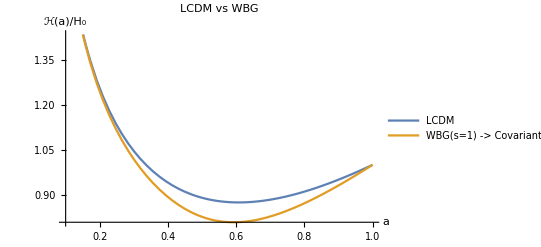

```mathematica
Plot[{HLCDM,HconfOverH0},{a,0.1,1}, PlotLegends->{"LCDM","WBG(s=1) -> Covariant Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/H_0",FontSize->20]},PlotLabel->Style["LCDM vs WBG", FontSize->30]]
```

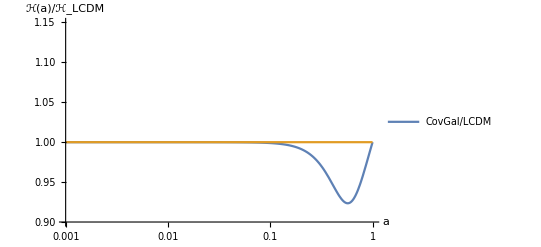

```mathematica
LogLinearPlot[{ HconfOverH0/HLCDM,HLCDM/HLCDM },{a,0.001,1}, PlotLegends->{"CovGal/LCDM"}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/ℋ_LCDM",FontSize->20]},PlotLabel->Style[" ", FontSize->30], PlotRange->{{0.001,1},{0.9,1.15}}]
```

```mathematica
(1-OmegaM0-OmegaR0)^( 1/(2(s+1)) )
```

0.911498

4 lines of corrupt data deleted.

```mathematica
a=.
XoverXds = ( (1-OmegaM0-OmegaR0)^( 1/(2(s+1)) ) HconfOverH0^(-1) a )^(1/q)/.p->1/.q->1/2//PowerExpand//Simplify
```

(4.4024×10^19 a^4)/(2.20431×10^15+8.20366×10^18 a+1156.3 √(3.63412×10^24+2.70499×10^28 a+5.03351×10^31 a^2+1.44956×10^33 a^8))

```mathematica
dataEFTCAMBChi=Import[FileNameJoin[{NotebookDirectory[],"fort.22"}]];
dataEFTCAMBadotoa=Import[FileNameJoin[{NotebookDirectory[],"fort.21"}]];
```

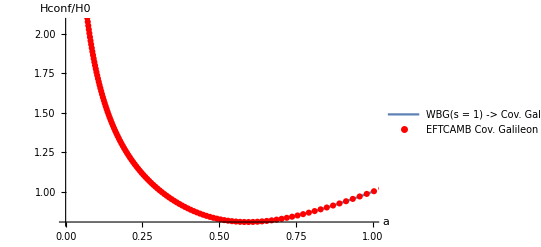

```mathematica
nbPlotH=Plot[{HconfOverH0},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Hconf/H0",FontSize->20]}];
EFTCAMBPlotH = ListPlot[
dataEFTCAMBadotoa⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotRange->{{0,1},{-0.15,2}}, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}
];
Show[nbPlotH,EFTCAMBPlotH]
```

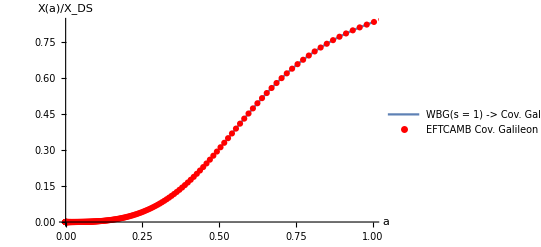

```mathematica
nbPlot=Plot[{XoverXds},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Χ(a)/Χ_DS",FontSize->20]}];
EFTCAMBPlot = ListPlot[
dataEFTCAMBChi⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotRange->{{0,1},{-0.15,2}}, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}, PlotLabel->"Chi(a)"
];
Show[nbPlot,EFTCAMBPlot]
```

8 lines of corrupt data deleted.

```mathematica
Sqrt[-XoverXds Xds]/HconfOverH0//PowerExpand//Simplify
```

12 lines of corrupt data deleted.

```mathematica
p=.
q=.
s=.
CovGal = {s->1,p->1, q->1/2}
```

62 lines of corrupt data deleted.

108 lines of corrupt data deleted.

```mathematica
"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "18"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.6248750920327548`*^100"}], "-", 
           RowBox[{"1.124206740626265`*^93", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "12"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "7.321750760777329`*^98"}], "-", 
           RowBox[{"6.067790877293509`*^91", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "17"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "2.4753833145160075`*^96"}], "-", 
           RowBox[{"2.3693861413663366`*^89", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "11"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "2.096118966751269`*^95"}], "-", 
           RowBox[{"2.412205738522689`*^88", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "16"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.4902913700852803`*^92"}], "-", 
           RowBox[{"1.839815998974751`*^85", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "10"], " ", 
         RowBox[{"(",
```

RowBox[{
           RowBox[{"-", "3.532558660467969`*^91"}], "-", 
           RowBox[{"5.300344804945028`*^84", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "9"], " ", 
         RowBox[{"(", 
          RowBox[{"6.366268130714669`*^105", "-", 
           RowBox[{"6.112943742276533`*^80", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{"a", " ", 
         RowBox[{"(", 
          RowBox[{"6.4586509645268615`*^78", "+", 
           RowBox[{"9.523007189741366`*^71", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ",

rscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[

```mathematica
["a", "2"], " ", 
         RowBox[{"(", 
          RowBox[{"8.055523951900114`*^82", "+", 
           RowBox[{"1.022066339411802`*^76", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "3"], " ", 
         RowBox[{"(", 
          RowBox[{"5.840596587014681`*^86", "+", 
           RowBox[{"6.242612597034636`*^79", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "4"], " ", 
         RowBox[{"(", 
          RowBox[{"2.7150350192233158`*^90", "+", 
           RowBox[{"2.3766703364489984`*^83", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "5"], " ", 
         RowBox[{"(", 
          RowBox[{"8.402408420141502`*^93", "+", 
           RowBox[{"5.789087130619309`*^86", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "6"], " ", 
         RowBox[{"(", 
          RowBox[{"1.734598654705107`*^97", "+", 
           RowBox[{"8.842575743421635`*^89", " ", 
            SqrtBox[
```

wBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "7"], " ", 
         RowBox[{"(", 
          RowBox[{"2.309983361171504`*^100", "+", 
           RowBox[{"7.785080206798495`*^92", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "8"], " ", 
         RowBox[{"(", 
          RowBox[{"1.8077594145920152`*^103", "+", 
           RowBox[{"3.046245326645243`*^95", " ", 
            SqrtBox[
             RowBox[{"3.521693145755

^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "32"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "5.3192800363152694`*^107"}], "+", 
           RowBox[{"1.1204361474311312`*^100", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}]}], ")"}], " ", 
      "Xds"}], ")"}], "/", 
    RowBox[{"(", 
     RowBox[{
      SuperscriptBox[
       RowBox[{"(", 
        RowBox[{"3.5216931457552`*^13", "+", 
         RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
         RowBox[{"4.367572272413816`*^20", " ", 
          SuperscriptBox["a", "2"]}], "+", 
         RowBox[{"1.43857713640625`*^22", " ", 
          SuperscriptBox["a", "8"]}]}], ")"}], 
       RowBox[{"3", "/", "2"}]], " ", 
      SuperscriptBox[
       RowBox[{"(", 
        RowBox[{"5.934385516424763`*^6", "+", 
         RowBox[{"2.089873745567855`*^10", " ", "a"}], "+", 
         RowBox[{"1.`", " ", 
          SqrtBox[
           RowBox[{"3.5216931457552`*^13", "+", 
            RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
            RowBox[{"4.367572272413816`*^20", " ", 
             SuperscriptBox["a", "2"]}], "+", 
            RowBox[{"1.43857713640625`*^22", " ", 
             SuperscriptBox["a", "8"]}]}]]}]}], ")"}], "7"], " ", 
      SqrtBox[
       FractionBox[
        RowBox[{"6.77248681876`*^11", "+", 
         RowBox[{"2.385022401318125`*^15", " ", "a"}], "+", 
         RowBox[{"114122.79839278391`", " ", 
          SqrtBox[
           RowBox[{"3.5216931457552`*^13", "+", 
            RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
            RowBox[{"4.367572272413816`*^20", " ", 
             SuperscriptBox["a

30 lines of corrupt data deleted.

121 lines of corrupt data deleted.

"1.6041901495422397`*^152"}], "-", 
           RowBox[{"1.620809335224764`*^144", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "22"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "3.5572901883766434`*^151"}], "-", 
           RowBox[{"1.6030386281405286`*^144", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "16"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.2928279311829152`*^150"}], "-", 
           RowBox[{"6.8089932726868`*^142", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "27"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "4.60107799304398`*^148"}], "-", 
           RowBox[{"9.585760546214332`*^140", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "21"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.3625074657623827`*^148"}], "-", 
           RowBox[{"7.841158286938557`*^140", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "15"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "6.398801343398834`*^146"}], "-", 
           RowBox[{"4.25548674657948`*^139", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "26"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.619006564200861`*^163"}], "-", 
           RowBox[{"2.6985292822259126`*^137", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "20"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "2.8087785988409617`*^161"}], "-", 
           RowBox[{"2.547604260572667`*^137", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "14"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.2194330274671845`*^143"}], "-", 
           RowBox[{"1.8566186663227369`*^136", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "13"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "2.8580461581262136`*^140"}], "-", 
           RowBox[{"1.3100349084582533`*^132", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "12"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.3024949939377275`*^138"}], "-", 
           RowBox[{"5.5348787523975566`*^129", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "11"], " ", 
         RowBox[{"(", 
          RowBox[{"1.394644556514619`*^148", "-", 
           RowBox[{"6.350368058586644`*^127", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{"a", " ", 
         RowBox[{"(", 
          RowBox[{"5.2289354498212934`*^113", "+", 
           RowBox[{"8.010227290591611`*^106", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "2"], " ", 
         RowBox[{"(", 
          RowBox[{"9.207200040851195`*^117", "+", 
           RowBox[{"1.2694092166640669`*^111", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "3"], " ", 
         RowBox[{"(", 
          RowBox[{"9.72731831238966`*^121", "+", 
           RowBox[{"1.192105450264652`*^115", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "4"], " ", 
         RowBox[{"(", 
          RowBox[{"6.851212176755215`*^125", "+", 
           RowBox[{"7.346779682971157`*^118", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "5"], " ", 
         RowBox[{"(", 
          RowBox[{"3.3778452342608054`*^129", "+", 
           RowBox[{"3.1047208371786746`*^122", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "6"], " ", 
         RowBox[{"(", 
          RowBox[{"1.1895536702384808`*^133", "+", 
           RowBox[{"9.111410309428617`*^125", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "7"], " ", 
         RowBox[{"(", 
          RowBox[{"2.9922667014068896`*^136", "+", 
           RowBox[{"1.8335461680374856`*^129", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "8"], " ", 
         RowBox[{"(", 
          RowBox[{"5.268834997068608`*^139", "+", 
           RowBox[{"2.421404870349977`*^132", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "9"], " ", 
         RowBox[{"(", 
          RowBox[{"6.184970569475509`*^142", "+", 
           RowBox[{"1.8949562687300458`*^135", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "32"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "1.2923471854909454`*^164"}], "+", 
           RowBox[{"5.9201109374589655`*^137", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "10"], " ", 
         RowBox[{"(", 
          RowBox[{"4.356241290519908`*^145", "+", 
           RowBox[{"6.673343590599055`*^137", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "33"], " ", 
         RowBox[{"(", 
          RowBox[{"6.863438180644252`*^148", "+", 
           RowBox[{"1.0463439027468178`*^142", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "34"], " ", 
         RowBox[{"(", 
          RowBox[{"6.677618645481353`*^152", "+", 
           RowBox[{"7.180990960888209`*^145", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "40"], " ", 
         RowBox[{"(", 
          RowBox[{"1.1472538245200058`*^153", "+", 
           RowBox[{"8.185661981954719`*^145", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "35"], " ", 
         RowBox[{"(", 
          RowBox[{"3.2845641756014105`*^156", "+", 
           RowBox[{"2.3857179474516794`*^149", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowB

{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "41"], " ", 
         RowBox[{"(", 
          RowBox[{"1.4969681045565992`*^157", "+", 
           RowBox[{"7.473643485126923`*^149", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "30"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "4.760545686987838`*^158"}], "+", 
           RowBox[{"1.2846240739918388`*^150", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               Superscript

["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "36"], " ", 
         RowBox[{"(", 
          RowBox[{"8.671042265581389`*^159", "+", 
           RowBox[{"3.812694818887115`*^152", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "48"], " ", 
         RowBox[{"(", 
          RowBox[{"5.267016097033261`*^160", "+", 
           RowBox[{"1.0320255239874326`*^153", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}], "+", 
        RowBox[{
         SuperscriptBox["a", "31"], " ", 
         RowBox[{"(", 
          RowBox[{
           RowBox[{"-", "3.6890511216227113`*^161"}], "+", 
           RowBox[{"1.1065842059617565`*^153", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ",

113 lines of corrupt data deleted.

37 lines of corrupt data deleted.

73 lines of corrupt data deleted.

28 lines of corrupt data deleted.

6 lines of corrupt data deleted.

4 lines of corrupt data deleted.

67 lines of corrupt data deleted.

42 lines of corrupt data deleted.

19 lines of corrupt data deleted.

39 lines of corrupt data deleted.

21 lines of corrupt data deleted.

30 lines of corrupt data deleted.

30 lines of corrupt data deleted.

30 lines of corrupt data deleted.

22 lines of corrupt data deleted.

257 lines of corrupt data deleted.

167 lines of corrupt data deleted.

73 lines of corrupt data deleted.

26 lines of corrupt data deleted.

6 lines of corrupt data deleted.

61 lines of corrupt data deleted.

23 lines of corrupt data deleted.

4 lines of corrupt data deleted.

62 lines of corrupt data deleted.

59 lines of corrupt data deleted.

8 lines of corrupt data deleted.

23 lines of corrupt data deleted.

47 lines of corrupt data deleted.

```mathematica
h0bVhm7Td+FHtmPYSlwQ4Xxnn/vIgTB4NvK43DA2
mOAqjoo/bxAGvvuW6+VKQwjsXqnG8DCIEP3KGNMWSjj+cOwWbwuDw1yq9IUz
dwmOPYNTOfNhIFb6LIZfJJxoUdLYwiIUDpoKcqKvL0cQtnaUg76m4fDjcvBz
nseRxI4YIeXp2HA4F7D6lCISTVDIKZdMH4bDrm/0JwXTYojLL819u5bCYVtM
rIW9aBzBtNSdISsWARNrvFyK1HiCvP8UpfRyBAysaeVcJSUQ5qoVb7hSIiC7
5KEXLSmR2OK050doVwS45smGit5MImoTwll/rkVAQ0mJ2JxDMmFCXRKzkYyE
mzeDOdrsU4hNw3ZavXaRoKsZ3O1tk0pUbu6zV8mKBOhmlLh+O40wFDsTSuqJ
BKM951u8M9OJdY3thXwMUXDEQOOyEiWDKL1++36cbBQsaLxuO/0jkzif+vXD
unMUxJ299a1TJptYaTVZdcmPAk3b3tDXnjlE4dgT7g9vo4Cpf1fD4f5cQodJ
9sRZpmiYu/i6aptqHvHreKl+i2I0GAp0GSUb5RP3jLhuHHaPhm0ivuukvQWE
5p3Q2IzSaLgr+XJv5FQB8aNosXLr+2h4WhRy7kNDIZH1oKXLiy0GBg/tHCmO
LCJUpw5/nlSNAc2Xh+gY3IuJ7zsyGS56x8DWprx7DSYlRJrMNoGO6hgIV6s5
I6hcSiib31KSHo0Bxsk0lkT1MuJr0GfzQq5YyDihvv3Q2XIiqfyiD4d2LITJ
6U2P6VYQp192pAX6x8KJKza2hFMlMflLunGOHAvrD3gMpRKriLj9Ra8tp2Kh
//kP8YKmakJW3mnuxb44aM7qYn05XkOMXh5iUbwQB93mftvqJeqIqDDNI9Wh
cRBoS0mqVCQRMjVUjX20ODA4ph45OkoiPr4Rtov6Hgf09mo8Ien1RNhqavCK
QDwsbj7mF6RPJiQEtuQ7GsWDLZfYkhpLAzGk4UEMRMXDnkzpDteuBiL4+vg7
9fvx8Fc3W4wxp5E4mqr/u2kxHpaPLSgoX28ipgdZojl3JUC176mrB4FCgEvH
Xu1jCSC3XXbz1f1UIuW
```

mQZgLQjf/utGduJr4kScvSrBPgx0n2uM9LzYSi
8Mzjeb8EmH+iuv/7KI1IohUaiqYnANgsOxWMtRBTOmbjl+sToPM7Lc1vtpVQ
GOFwT3+WAKNXIiwaf7cRCTef0r2cTIAE+5o+3U1ITDIGxTPSJUL8P29RY5H7
hHyq7QElnkQoN/hl5n/kAREnur/GUyYROA3F7zk9eECMtb5RqDmXCLYPL/Dc
vNhOyJ6P7p5wTIRAY/+Vjj/tRMzYf6b7QxKhdzCInlrykBj1XJ0yyE0Ep9sy
l6rOPSJOMJG9oqmJcPp06mrx0iMiKufqlkevE4E/nr7CjdRBfDoukLI6kwgh
beR3TDceE9KPBg9KMSbBR7oPiVHHOokIvbb6q/xJkLKqt7I000l8mLipXHAq
CZZPzP3uan5CSHqLvRw0TALjyY+pkwldRNj28UvsrklQ/R7+vHB4Sry7l/VN
IzIJes54Jt9V7CaOS+n7BhQlQTernzzz/mdE6GMmZiqRBP5+jz9+Y3tODJm0
Z8wOJMG7Nh1VX/oXhPg3bxHhhSSQvnSTh7b4gggOkKBcYkmGb1PfGCrHe4j+
HbvUUoWTYdTAdLH350tCrODZm+fKyTAj0yNoHvKKCJQJsd5sngwcyUq9Sdtf
E2+fnPqh4JkM2/rDfDmTXxOHzRcCbsYng1swOzVVsJfwn61grapIBoHMYkst
7CXeBF3JHXuUDG/fq2sfN3lDiHDtPcoznAzPBKyytH68IfzKX7Xo/U6G3Ude
22dFviVeK0RoRXKmQCBjKd3MiT5CqNt58MHRFMjgNdb8ON5H3L4k6PBbPQWa
pMK4ZxP6iZ75d7+OX0mB8yOtDXyKA4RgaFKog28KHOHHzN7vA4Q3t/bOvNQU
8NvXsS2YPEi8qNxU2F+XAof0wlJlvYYIASWaBGt3CryRbKH+kntHeL2+cV9t
IgUWsxc/4uo74pmt6Lk7f1Pg9H6t+Ygn7wm+358+NO5JheLjm9Tmij8QHtHp
zt+kUiGWW4FfNegj0bXXd1VQNxXW3hmLhlsME7w1UpHmDqmgzyj5mzj5iXBX
nuZODkqFPdWz17nZR4gnbwpKu7NTYfCkyPbOmBFin4PpCXpKKgh6rLR93DZK
3Fhl75B/lQpSzFvnL4eOEo9ju/TdplOB40cR87l/o8RegcDR8s1pEGo25ysR
PEZcb5S9MXIgDUxuSwaRWceJRxpzf7nl02BM+tmVuKxxgru/N/a8QRpcLjIp
fiw0Qbhcjdoffi0NRC7uemZKmiDa11SqMDwNKtgKrQqUJwmuhBX5pYI0yLQY
t2P9NEk4CdZ3ibelQdb57Xodfp+J+xRHY7v+NOD6afWkY+8UsVOb/3POfBrU
5xU6clCmCMePAx5vmdPha8QMWVT/C0HciGdgEUqHzGKz8pHNXwmOzRpJqpAO
oyPN93ooXwn7pCMCvqbp8CRr2eKnwzTRIjRWR76ZDlQDkyKDPTMEGy1TaTo2
HcwHko/OPpkhbHX0XgiUp8M2bk5xjfBvBO3TNgvTh+lwUdFLgffCd2LHzQfT
CR/SYXlhr8juPbOENaO3T9dSOgzY1byV/jRLUDOPb6PjyICVv6MHvUvmiO3i
U2myYhlw3N/AqfTkPGH14J6Qq1oGBH5iOcZSPk80ngtuLL2cAd2BNZTlPT8I
pjF51WGfDGCNCGB2ivxBWHr+eM2VkgEDzS+O2q78IBq2VVjp1maAweh53inH
BWJrjtVcaFcGiJ5OmPk5vEBYHN/j3zaWAU3HiJ+RlotE/cOXLD/XMsCIWf5D
xsdFYotReLYYdya813/QctDiJ2H2VemIjWQm7DzYVyL67idR57fUnHU2E6T4
Q+uqjH8RDNvfafTaZcI/+gHq+ZFfhMm9xH6mwEzg8FyxnHddImoktexUsjLh
ebRD2frfJWLTY7qf3o2Z8NvFBr1jlwkjk+ZgUk8m0GvlvLDe95uomnHl+PIl
E0QH2P+0lf8m/vmL5PMxZMGjdYJxSHWFMOT8dMyYNwtOrjdlFUyuEBUlaUSc
bBaUfPi3qytslViXO6fTqZcFefsP0HRF/hD6TyTfrztnwQPlx53ST/4QZWZf
r54Iy4Id5jK3fe3XiD/f83+75GeBqvm/Q4d3rhMXgkzCi1uyQPSUQYX/03Wi
ZBf77g9vs4DNllYjEPCXWCl7UrxzLguytvrH7ZT5R5xTCJA+y5QN+591Fl38
8o8o6jn5MFgwGyREB/N/6tLh8pXZCy2K2fBaVEuUp5oOdX6VfPphnA1LLV5y
U5ybsCAk8vph92xw0xz4rOezCX/tVlm3iskG78n9c2afNqF25e/ojNJs0B/u
YmZQo8c8RRLPqwfZwKug9UO7kh4XXzlUbH2fDVmqu02k2RhQ05ZPDn5lA4eZ
S3FMMAPmLvd3erHlQNQXfk2eJQb8ERV3sfZwDtxR6xE5fXUzqh9Qn5hUzQHC
pnP74vvNmF2/7s5rmQN+on9pcG4LzsHopoveOWB2Omnp4IMteOZNRkJMUg68
SIv4vSrHiJn2F/g6qnNA71xrtVMrI35f2Vr7pzMHfru1X7RR3Ir/xd4/LT2a
A1WMHM8ncSum89965vQnB2y15iYXYBvONBwzK+TKBb+rZ25FP9iGyhqfvwwd
zwWVhH49kjITpr7LvcWhnQv2qjWFdT1M+PXaRUYt21y40q0e5XOFGZXW5FID
/TfW+4oQDxaZMTl+XrA5IxfG92gIht3djlMHy8lz5Fw4kypZ2L2bBU9TLquI
vMiFjp1beePLWDBRi/uV5VQuZM9RPN7K7sDJDz2WaZvuAd8hr7nZdzvw1I2w
7y/23QNCS7FFLpAV4xmU/LacvAerik/7Fw6x4XjaL2bFC/fAflFA6cBTNpQ7
UpPp4XQPSEXmi5dOsmNsc4Jodeg92B4kYf05nB1Hz2pSx+/dgx8k8wnRIXY8
+emf2j7aPfimlZH+XIYDo92pb/Xf3IOIovMnviZy4KctrjZR3+/BZ50njyiz
HCiTKbzQvjUP7he7d504y4mRR4cDVwTyYMRLssu+jBM/3k9lkzydB69ZPqlp
M+xEKQPde45GedBo4PNoxHInhn/eLJ5/Iw8OhvEPRT3aie992loHovJglGPk
R+DRXSixLV+brSQPxAT4fvCl7sK72cZD6vfz4NrqGQfH9V04dIzN0X8oD95e
aRwzs+PCYw87l5oW80Do/sL88nMubD9y/+ESYz6MLwfyKsvsRpefPFGcu/JB
7jf/da783bgbvfSOCeSD0ZhmoNdubnwQ3rtH+1g+fFGfDb0Vw43OesdG7BTy
4WD74O699HuQa19UWZBmPuiYnn5lfmsPwtif67kX88EhVVNL+dsenK4yPkmz
zocIx8y9T6z2Yopnw/pb13xIIkn1z7/di0rAtuEH8+Ed6UaBlxEPft3mHMMS
lQ/buoad8t/zYHJvp4Foej5MMHG/sbLah4o5B/edKc4Hab61wOaJffjFzn/s
cn0+RGUP7il33I9Jx99V+GI+JATYKEl824+nV064pT/LB4nALcl6rrzo8KBM
rmEwH8zKXLkPLvIiRxTDhp/Mh6Lgj5t8Ig9gq8HlJ9ML+bBHatrbnI8P7Xlb
4xjpCuBW1w2J7kY+ZJ/abXRwRwEMvdT8PnaIH1tI7rxKPAUgzfE3WcSVH+1u
90yYihTAnN2yjTSNH9nOHKn2lCmAhO7XDYwMAkjbEXYzUaUADEcnaw3PCaDt
wOipmnMF0BMQHf6nUADj7hnQPzUvgDuc/WbWywIo51j3dMKxAL5vuRcZefYg
jktuT6TzKoCdba433fIOYuwfe5P9IQVwmo/vFs/iQZR9/JBPLqEAthQ+WQhV
F8SxuAMb/rUAqszKVOszBTHG5Hata2UBPBdTzzH9LognD/Z7RlMLgCPwX2Kr
ziEcnZFULOsogJ+7FdkGqg5hdFPs5kevC6CCicWvmlkIm/z+PRseLoAdwdvg
9FUhtFI3T16d2eD/5zKGPRFCZnaq2e6VApBKs74cIySMjUOcG/63EAq15cN0
Q4TxctH1r7o7CyEzwCete0QYma51k67yF4LvWccLm7VEsOGksPdd8UKIP9UY
ptQogpZ0wVBwqhDel7TcFeMTxW3dHxkJjUJgLDnX9ixSFMnJ8j2DhoXAMhiV
wfdTFD+aVaX+vFIIT3PDw0UsD2P4oa0b/rkQ/LU5fo0/OYySs9aHjvoVAln3
pc5FySP4gYozGpGF8NJPLm5b3hEMC+JpsEnbmEv7XlvjFkOJs163A4oKYe/D
Rd7sBDF8v6tXJZtUCI+Lbbkntx3Fu8PiTFSiEFilr756F3gUj5dHvurtLgS2
kCz0+30U37lNps8OFMJJ6SGjZ67iuFne+DLzZCFwtQ2zPPksjrX0DcLCC4Xw
Tj7c4MalY2j6nHVW5V8hSGfYtAcPH0OGNKemSyxFcCXI9n6x/XGsudzp57O3
CFRa7h+7OnscTQ4fPJMqXAQpCh80vpySQPrFO9vrpYugtO8J6Zq/BFa3DfU+
V95Yv/k/jsftEmgcdiLri24RjMT2l81ulsRNFxKvbDYvgu1RheRpDUkU42Y4
zO9YBArzKq60KEnsH7GcV/AsAt5ChrMubyUxsLKFahxcBFsHqOk7BaTwiMfu
Db9fBAKHfDzCr0lhn6K7enxOETiK7xHuoklhwNaeHVUVRVDxZWm+b4s0Hn59
uK+TUgRW6q/31OtJ49usuzljj4pgKOLniGmuNPrbjtr8fVUE7pd5Yl59kUbR
Y4piPMNFkPnZ0YJLRgYNftUunJgpAufG3SMv78rgOjJv5IUikB3k2Hb8gwyW
RdgHXdtSDH6U1ISLUidQX/+hZiRnMRjTdz1SjTiBa/sOsJfwFcOpZa6ZlY8n
sHTSZ+DB0WIoVzQ97y19EvXq+u59kC+G2kYB+fsRJ/GPt6T9b/ViSHFhm+/5
eBJL/osV32VYDFEHolvLpGTxAsvXn8evFIPnd+127yhZvP3GrO3s9WKovFKs
Pzgji4dyKSEOvsVQF+jov6Ijhy/tOc+GRBTDoI1WyocaOfSRuM6Zl1oMXxm8
x4NY5VFw9elQS2ExUDoTW75el8eeR0IF/XXF8JQlzmHXS/kNTxbkuNBWDG1F
r2Tpj5/Cg8Yfj7N2F8Ny5TnvhrhT+IJffvnwwEZ9YylP0dlTeGs6BdUmiqHp
kAzZ1VgBBRrn7175UQzBjDT816GAOr7Wunf+FoN39JLOWanTuHQGd2VuL4FP
3BfI+nmnMZ+VZyPflACZOUR1N4sinh30LHolVAItu4YN07wV8VfBa6dvUiVg
EdUr/2ZCEfOcxaW2KZdA0FK42osLSqh9InJFULcEDLhOdoe2KeHPvxMPwKwE
un6W7F0VAbzXpRxh7lAC7qaFegyFgFpJOedveZSAuf3dzFpWZbxpyrqRj0og
ZjP91AkdZeQVdBqujSsBa9F999MjlbHr2+OS7uwS0JnXO/+2UxndKQLXPpeX
AKf3244ZBhXcH3hHhp5SAoODd3SGlVXwidbQH95HJaBp/Ymz+o4Kuu088Uj+
VQkwzx06c7FFBfd9TIi6+LEE/J/Ks7xbUsHO0m96btMlENplZ2yt8B/euKG5
N3a5BAaCmMw/BP6HWbItI+WbS6E0yePX0c7/UG3T7vIOjlJwM5wyNtyuinPd
bq4jB0qB7cD5Bv0LqpiZ8uLkmlgpGLyWlhNNVcUzloc38lgpdN3/sLtvSBVn
Re4+llYvhScxBwNMD5zBjB8jMecNSiE+tDS/yfoMqraeNnS2KgUxtezKr6Vn
8Htoxr7wa6XA8+a25tUfZzD93M+xwtulcO/P/Q4qqOFDLvtKDC8FPVGF4sFY
NXT51O72LqUUKrfz7H/+Xg13V/Bu5LlSkHy8ZJV0WB3b3X3oOOtKwdXDuUzs
ljo6n+57It5WCulaBQczOtSRi1EyXutpKViK9jMOcmjgg5cxRnb9pfBLWTp8
xlIDnTK/8AaNlwKG3+3vrdLAXTZnJnPmSyEh0/nmwIoG3j+aX928Xgrf3tzV
E9LXxK+LHBt5sAzywjwmlSs1MZm4pjDPXQamNl0OR+i1UCn8KT2LUBnkG1/n
GDPVwi8XhLpFpMpAkGuZx7FeC5N4ghJVoQy+9p1qa9umjYoTH0wu65TByhsO
8ZHL2jhVI8fva1oGta+zi3sp2ph4K2Uqzb4MbBN/m6bsOIunVeZryTfL4MWl
+BAh27P4mVnHqyewDDromN8I3D+L7L2E4nRsGVxf3PMx6qAOtmbv3cKYvVHP
vqWo7a4O2tl5PhcoL4Otu4/ZUr/oINvx18mKTWUgEmRs7ntWF1t+HzU3fVgG
bKQrj7fV6qLtw4iDni/LIOvzm+HL7OeQNWbia8KHMvg17zce6H4OaReV66u/
lkGJ4E1Wl7fn0IYvx7trqQzE3zzPEjh5Hnd8XYYJhnJw/DD1sCD9PMqRrm6l
4yiHUo+6za/Xz+OYz+OefQfKgc55NWry5AWMURXYyK/lEHbfVrzj+gWU3XHn
koFcOfjKtUWFll7A0f7BQ65q5dC4lv1IePgCRufLfIvSL4et0nm/K7n08KRT
QkPp5XKIKO/X4tDVwxHpb7cfupQDa+jHAdNQPYxa1/hv2Kcc5uROPQxt1cMT
T4qYVsPK4aLXS9GkBT28HMe1kX/LoSbx15Hgw/rIZOKWIVmwwX/m61aylT42
Cry4rFtbDuGGpNJnefpoOSMqcrW1HFTHHnQ/GtbHbU2hs6Fd5cDQ3JmexWuA
Df4jTfl9G3yCGiUuWBjgJc3Td9rGysFnW1XzRJYBbuXMODM4Vw5pv3P0TYYM
kPx+cfvPtXL4WLTAX8VtiBYl59+wMVeAjsUu9Y8XDTHMpT1LjLsCJm46Tcwm
G6LkSV5rjUMVwFrmxTvy2hDf//M+bCNZAYvb1XbWs13Eu0/fzvsrVcB9vcMj
63oXUSJZYiNvV8CNoe19/zIu4juLmACKSQXcyjqx9eOnixgq/EW9164COMwH
clKFjfD4vCrrrHsFtIantx6+ZoRDtLw+psAKYHSdjchsMMKQkD85QrEVkKUi
fGRyxQhrta/ZqmRVwAlO8w4WZWM02fVU7FJZBVT03fZjDzNG+uFDi96NG/zO
cN+af2aMNWWBLSntFSD8J3mwmsMEjd0+BJF6KsAo2fCxmrEJblKQ03r+vgI6
+5/9qC8ywerNKexfvlRAc+in6ZJFEzTqmRtgWKoAqnDxbTdVU6TLOJvHx1C5
8Z4d7d6VbIpVV8rsFdgrodu6d1PCmCleFGPYyPuVAJ4HtMclzTBgweOX+5FK
SD9H7mYNMsMjba/a4mQrQegvrYrzlRm+vXs0tPJMJcTuq9g1d8Ac/c9HnO3U
q4RbSotHi6+Z4+G9E5xjlpXwtDhon1SbOb4Zg3frzpVgWOm8NZPZAu9UZxfs
9amEa7eCDmhctkBRr2XHE2GVMFMW4GNGs8BeMJDQS64EmSMnzVV2XsI7THXL
LvmVcD/vydwfl0tY9or/fkRNJbjvumEd1XkJ9bL8wopbKoHh1ZPhb3yW+Mdm
UPfBk0oIKayNF/SxxFJxGa4Pbyth2kcq/1ivJV5Yjv+wPFoJN6f7T7GKXcbV
BzNFO+cqwdnpR+TDkMtYEqXhfHytEnRlfKlnP1zG84ZFUmeZqkCrnbJkyGOF
q7z/Vux3V4HhqTJvbQ0rLJ4yaw8WrILnyaY9rLetsKf2ecQ9iSrwCXApbqm2
Qm9v0QstilWg7VTGee6TFQr+F8rdr10F7g4aEk85ruCL7SPDP4yrgI7as+vo
mSt4q0+hdIddFUhcshnw8rqCB/PSrx12rwID5fW4ivIr+NxxUUYtoAqKbR/q
d7zbwEudX7OKqYK0EDv5JyzWKLBW+cgvswqKNIJNyUrW+OwxY3RGaRVI+Yw9
vXvDGn/FeOs3NlTBr1u1+SqF1phv9HbvqwdVcDrv0SvuAWvU5pcYnXlRBcpv
A18pstvgz6/R5VvfV0HMgOakppYN5jVMuQp+qQL7LYai8sE2qHVHVRZ+VcGB
qkdk1lYbXFTP+2tGXw30u2m5Txdt8B77n8debNUQas9O73TUFjXfGcUm7a8G
3tq433O2trhYRDasPVwNDq8bMs1zbZHX+dD+7pPV8LVX/G91ny0+kQkcn1St
hktOskoTO+zQ7e/7yk161XDT8qD7JnU73N8l685rWQ1/NP/Ub/a3w87EZHl5
52r4fD59xJlmhzfM5+guelfD/uwrGt0rdrhP6GzXjbvVoBQ1wbH9lD0+ni2N
j0mqBlqxkPmx2/Z4o5neuDyvGn4EqijJtNgjT7DlgY7qarhYqti/f9Uez2i9
mvxEq4Y7Vo8Uv8g74Czn0Zo/ndXA+s02Ps3HATM/hHtwv60GqlfupAjNAVVL
xxWkR6tBgu+1Wc5vB/zuCgznZ6tB6/MJpp+yjpghn93t9GeDb+0b5uO3HPE/
huXEsG01QKcU6qNLccTvz/VNC7lqYMLZd4FnyRHT02r58WANqBG7LEuUrqKK
FfOXoeM1kPhqUpwt/Co6i/jV/TpdA1zt1gEmL6/i7h8DXhzaNeCoYukaxO2E
D1qklcSNa+D7uQP7oi47oVNo/BYt2xowd5XIcy9zQq5zM89t3WrASP3CHoU5
J7zPrZES6F8Daabbi8ZPOqPTaKF5TnQNTLG3m7v4O+Ouqr8HmzNqQK4s2rLv
sTOih9n0m5IacLbPeXJghwteVaLUz5FrIM6ii6xp6ILJW0R9tj+ogZaIFwoG
2S6o+DJEWeRFDdxJ80n7+9kFpzI+bVV9VwNKB0LCSuSuYZK1wkvLqRqoTRsu
Eo26hqePpqfd/lkD52QpOyLeX8OpXwuX0jbVQuRF6/FHR69j4v1zQmTWWvi2
d0n1w53rqBBZ+e3Fvlrgjjc697rnOn7WZ2z8KloLDwpOCRTxuWLCfmvfLSdr
oYlf7L3eDVdsGX/zn4BqLTx/lpn18YEr2tYcZ1a8UAvXJNeUirbdQLZb0a9N
LtXCulC6XqfEDaQpT2V4ONVC6l3RXYMmN9CGWdUq4VYtdPpmpA4G3kDWt/dE
qkNrwWLXXPe9qhvYnLs6+ySxFr4KjDzIHNrAOxhRxu/VgmZ+BkPQVjfcIUm+
86+qFmqvDRUZnnBD6uoOtX20DT5z18m7bNxwtD2ARbazFkZ+0Su3J7hhTPT7
N/pvauHoebhkhm548qJs9vWRWogQSuEZmXHDkQPJ1lHfa0HnyJ0I/b3uGP1l
9nDpai2YextQ69Xd8QRZ+0f71joQKLKlrt90xxHf0uaPu+qAl/9VxskCd4xS
ow9cEaiDzpvPnS163FGGzVKD63gd1P/SVnb9446fBmmskqfrIOEm7Wvg4ZsY
WcjVr6NVBwqs9NJ6l25iw9XwXEejOjCaPvdse+JNvCQ9bhtqUwcenS0dpI6b
uG1d6Wj+jTqoGzKUVP59E8mdWYutd+qA1MEk2CLmgZcSlloGourgoGhn1YHL
HrjVTD94Mb0OHoVpfryW5IH1grVabCV1MPRe9WnZYw+0+M7EIUbe4LfTMOj5
bw9kpNoNqt+vA/5kJu4PYp5ICmzPs35eB+l7W7P7LT3xnYa0g/9QHSyujfK3
JXriXY74Y1mf6+CkPZka0+GJx99P/2parIOxJUM3zWVPvKZfNOxIR4LBAseB
PnEv/E9W7+ESIwm4f1Y+E3X0Qu79/0pCd5CA8ufdtE2hF36jq4nk3EUC8VdX
NMM/eGH7pNm1fB4SLEWULyftvoXp3dv0jgmQ4B7f9PbwC7fQpY4i0yZCAvTX
zrCJuoWbkl33aB8jwVzC9zrRjlvYf4t3bUCGBLbZhF3/+i2ssnj2yU6BBM+d
SM9dZL0xUMXn0aIKCb7VxC7P3PBGI2GRsiBNEjDHcKwYVHqj2Pa+KLbzJLjD
OzpePO6NdPPB13MvkqDa4mb38H4f7HsroS9mscFP3+j+JiMfrKQNn6BZk6Dj
cliPQ7IPBtyL2atxlQR7p93d9/T5IFew2vpbVxL4Rrh8qt19G6ftF0esvUgg
89TkiJjJbbx/tqBj3o8EKWKMjrGZtzFF4ny5f8hGP8dUa/re3carXOvRLFEk
+P5OiHXzfl9UWq10zUogwZZa5fw9l3xx1ycTA9F0EpyQ++G1854vfn3EKEvJ
JcH7r7OlP4d9Ecsbec4Ub+iVy3ymjc8Pk2Ot/76uJAEjm6uNk5UfirrtG7tc
T4KpYMY9//L9cP3i08ffqRv4qxFet0f98M2pWxW+SIJIA/2kDwJ3sJxPKJbp
MQn+5r0tvWlzB+9sfnMj/RkJfmXFuN2uuYP6XwMNhXpJwPPnoaXt8h0U6Tkm
1zBIgsMckaGSKv64Rv6wT+UTCaq8bVZGo/yxNz3qX88kCUyDbd54vvXHMj+5
cYtvJCCe7jj8nTcAT1v96JxeIEGnIR27pkMAcqjlVXqvkGAN798LIwXg58O6
cYx09aDHOj1dvhKArax/3FIY6+GBluZdY4FATFwsv3hwRz0MbXaNfK4WiPaD
RvKknfVwTaE5RtopEBWIzbxKPPVwc34hMyYuENkLyXTP+evhs/Bs6wA5ECfD
rCZMRerB5DSs7xoIxBZn1q4p8XpgLAwJ81kPxAvnn1R5ytRD4rI0m5BIEArJ
eMYzKNTDpj9/Wx5cCMLVPYI3E1XqQWf6TarO7SB8uf7KiE+zHo6e46ruKgrC
4jH/UzXn6iHNlsx04kUQ+jw5ekDhYj2Q+UVaEpeC8Hz1u01PzetBcXv/02G+
YDyUGDFpZF0Pq26bzuzXCsYVz5NPJxzr4T+5Xhlt92DsMZuodneth9N6HWWO
2cFoo5SbQOdVDx9XO8tvdQSjnOBZjzi/egj6OPbfre/ByLptxXh/SD3wym4N
dtgdguPfShUqI+thYLXOTRNCsPm1IZ9cQj14evHx8jiGYCyFnqEzbYM/PU27
JCkErbNJnw1y60GpwImW2h6CsoGW3aNF9bDmfaHRYz4Ed9ix1LpW1sM3C2XN
//hCcUyrJXGdVA8Svv1Bf3VD8Zb4Tc9oaj1QdA5er/ALRR1OAdO9WA/O2tI8
qlWhKLDcc7qsox62rzsnPRsKxaX3fvwnntUDLclx/L9td/H5gyObH72uB+tQ
OZ6Kk3exoGRw6sJgPVg2bVb9a3sXvaLCng0P18NLg6tO/yXfxbOuMnUuk/Uw
GEuf69l+F/kNx5JWZ+pB9pvUVPrcXfwll+AVsbChp77gxQreMIzer2W2e6Ue
9s+6LlacDUOrTcuKxf829l/f2pPpE4YnPhcLSDGS4Q/fi85/1WHI/Ex/ywMW
Mjxf2NT2ZjQMP9XRfdXdSYaDgdxhKbvDsTGl9vn7vWRoiE6Q+u9sOEb5WJCu
8pPB/mnOyw8B4XjZkjllWZgMC2voZNsYjjKqzbfuipPBI76BY+hLODKJ2pvv
lCFD0Zn116d4I3CYZRcUnCKD3atntEi9CLw5//zgcRUyqDL+6nt8NwK1+m4z
EhpkwJ/XZeZoEXigRXRa+xwZRFqCx7bMRuDivf4Xg4ZkeO3h853pYCR2hYTW
25uTgVU1x/rPxUjMdZRK/XmFDKlfrp1/FxmJ7roj3sGOZNAfXn9QSkSiplSc
BbsrGaRzzTusfkQiL/dp5XueZKigt3ffdTQKF/58FTzqRwZTE8vhRIcoDP9U
uLUlmAxlfp9PrBZGoUXHhRmNyI3+LM9F6A5HoWTF356+eDIMFLhPRO+Nxq1x
1WSbNDIEqi2ZNBlG4wd3s7QfOWQQ0PT7+TQ+GuuNt90OKCLDK93Rx0+7ozHs
NOXSjkoyDNbFvW/cEoPmArYq2SQy6HFeOROtHIMSjJxCh6lk4D8cwarrG4OM
M/e3UQkyLC+Uaq42xWB2j/e3Mx1kIAS/0yXPx+CNBuFXvd0b+u3qUOMWi0W1
jLcNVq/JoMaXKhRuF4s8d4LTZwfI0KdnVDuWF4tzVyR8/YbJYGAlO3v4XSw+
Vh+2ZJ4kw+V24frsvXGYJRbzX8YMGaYb6PYXWcShK/spYeEFMkQcz9ZPzovD
M7+mmBp/k0F956Kty1gc7n2X+l3lHxlklbbYHBOKx1ri3OuXWxrAKb7HYsgh
HkML1xovsTTA/ORZ62uV8WgaXpkxw9kArP2MIdPf4vGYi4mfz94GoOpccSjn
TkAGPUarrfwN8Emm4MgruQQcPNGomircAAXftyZ/M03AGh5rEUHxBuBXMStf
v52AIf/YttdLN8BzYWV3hpwENJkgZpVONYCvQvbv9bYEFH/q3PtcuQFmipb+
+/4xAR9WH6KYaTRAjPGqyeu/CZie2Jv5RbcBenTP/VfJl4guXoF3vAwb4KB/
FqO3ciL+Z37symbzBhDbpRCUaZeI3MofziRdaYB/b//2GEYn4rdDUaL8jg3w
8LqBBUN9IrYzybHUXt/Aq0xIlvQnYtrs5JyCZwPAEJicWktE5zfJb576NoDe
j4GBhwJJqNKsQjUOboA9X41pShpJ2J+9mjUZ0QDS5bu21LokYVVguf/N+Aao
aM15xJ6UhIF2Rtab0hpg73a1dXtqEl7U3qwen9MA/RcCWkgfkvDIcfJh3qIN
PQpCGGY3JSPdLqsdVRUNcL750cgBkWTs+73jhxypATL6zcxUdZKx8mPr205K
A6xRWrzN3ZIx4OHVZkOiARqy/6o6pCWjYRl3ztijBljpVOmwb03Gr1GvAm50
N4Ar/9Ams5FkvO/qb/P31cb5/VZIv8SUgimGRzViBhogyP6w57B0Cl6Vf3eE
Z7gB3ngKnNWzTEGlAxGs5RMNkOTld5ASkYI7GU4unJhpgP92mm7e0ZCCX6bG
+x79aICn2WyrFz+mID5PpOn93ui/BVkSt6Zicj3kfvrbAGQNRzWUTEXHtO+B
17Y0QgMPa81H81Rc9ym1/bO9EVJCtunO3U3FXktDzUjORmAZoz+2WJeKZar0
R7n3NkLuyD7Tr0OpeEeUxFbC1wjcxhcHXjOkof4Oy0Up4UaYuHWrvlo8DUUW
tg88ONq4cZ8d5n2M03Ctn9ZyTroRpp8z5coHpeHrVod7H+QboVJO5MFMZRqW
5XMFOyk3wp4ZJ+uEt2nod/eR3W/1RpBgbYzf8y8NOa76aYXpNsLLvwGsdMfT
8bPuEfFdho2wLenxnkHLdGyVGmQvNGuEknelzflx6ZjAHfbz+JWNeX7vsimm
o92a9CDh0AgHDp0bYZhNR4XR0daz1xvBo3eT3z3eDGTvjM8b8miEsps5bw/r
ZuBkpWKIg28j7PNk/Fnil4Et8TP2v4IaYf/z1+Oc1RkY75GpHRLRCBY7u2tu
vM/AQyb6xzjiG2GI8575feZMXD1Nx5mXuqFn0trSX/lMfClQ++toTiO4jylG
Hr+aicWMFkMthRt4V+39ehmZ6DPDRGhWNMI69RLN5kkmnntFze+va4QjJCYn
h6VMFGyyC7WlNEK17oishVAWrmTudFxoawTaDt6j/xlmYY9/+9nAR41wlME9
dCUkC4tsXI+zdjfCt/M6Vt9pWeitybsz51UjZFq7nn41l4U7jvYvHR5ohJ2d
BoKFQtk4xh76jvqxERgvTPLZmGdj8y9JVJtoBIPonNM7E7Mx9t2ngjfTjRDX
xxpK7sxG6/uxd6/82OBrOUunspaNssUKV+eWN/TZcZtAyRxkifyqc+dvI0ix
23aIOeTg2LV0ie1bmqBFd4YvIicHqfpquzK3N0HahYh3b17nYIzs4rIwZxP8
fJX2l3VrLgrsq37fuKcJGMLd0+RP5+LSP9P7//E1AZiYVRu45eKzia1Fr4Sa
QPBIrPal0lzMf9oUZnm0CbpOs/savc9Fr1obp29STcCyz0IT2O/h2WSOc7fl
m8BIyrSNW+0e8nvfl9ym3ATXUw+PfvK5h78srnGlqTdBPdvP9PaGe9itsm9F
ULcJLF9McfjO38N84acf6g2agJsh5JOAeB6eYA5+AGZNQPWyZKFczUPmuePF
L6ya4FxRXpFsaR5+evMx3NyhCWjnPpFKx/KwsTna+eu1Jrg0XpcXxJaPkbny
5295NMEEl3JNqXg+Xg6ektri2wRv7NrDHp7NRxmH1N3JQRt8Ejol+67mI5OO
6ip/RBNYE/MNw+H5OCzx42NtXBPsVO7g/FSSjw1cee2nU5uArmLeoP9RPmqu
GJd0ZzdBqc9Hv47RfOQd3hJpUtgE0oxsyRX/8nHxYYPL5/ImOM6yJ+cubwF2
lV254FHXBG5e13NNFAowN4ZNhp7SBJ6dPjkHTQvQ3Y3gTmhrAo6punvjXgWo
YeT8h/dRE7SbeldkpxQgr8LeT1VPm4CkdPCIS1MBLvA9eSj/qgm2bs6Kzh0o
wCebPUuf9DfBEcKvvGOlAC2+iEdd/NgEvGrfw0b3FaLki/fXxseb4LMXq/hP
xUJkJEfquU03wXgaR8Ha5UJ8nyZ74t98EzjWrH1ZDSrEet/JPbHLTcB3dIJ5
rqgQw6yS13j+NgEl9APL0ONCNFdTGSnfTAH/+zM/m6cKUeLI3KOT2ynwbIL7
aRxTEW5hyy3r4KCA4hHteDOxIny/qB2tv4cCgZvSdffrFuGNAQbXkQMUkM6f
Ynp7vQjV2ur1rwtRIK93d3dQQhHyFFw+uSZGAa6CIylC5CKcu7uDJ0qKAsHX
567df1OEHU6t69zyFIi4ce7S+V9FmHX+6mgJUGAX8y7Hvt3F6CrD/VhanQLX
tu5L0ZMrxjN7H5e362zgrxj8t9u8GPf+dY85b0ABg4mKq7lBxTg7xn/joykF
sjy2q+4tL8aQziEDZysKiMmx9kX2FKNJVbjsij0FIkXshOd+FuOxhBP7wq9R
INSxVFFrXwkyeI7/3eVBgU8TpwUyVEpw0DRxrPA2BQ6kvh9471CCNUrQKRFE
gYqVYYddcSUYLPi9AsMpUFUwM6DSWIIm27JjdeIoELfD8pjtuxIU/67p9i6F
AtcT6tx86UqRvnfJ0DGbAk53TMvDhUsxvalObqmAAkkzFYMROqXoknVpf2g5
BRiO8TAFuJeiSsB2Os46Crw0/w1OGaXIbUsbz2uigNWv/BBtLMVvmg5PxNso
IOB74x3fRCm2i3NVtT6kwA3JDO1ppjJM43wUp/WUAtQMj3cVx8vQefmG+8BL
Chj9OplgebEMlT8cMLLrp0B60/nxFb8y3N3+XH7xAwVCTs18sigvw6riu7xB
4xSYTxO73vCmDAMjpTexTVPgMKts6vrfMrx4fXQiZ54Cd8alLRSOlOMRg/iu
I8sUuBsu1u1ysRz/ySpWN69vnPemvZ8TA8uxb/9MvPpmKjiI7aJWVpVj5abM
m2+ZqfDSU/gMtb8cAz6rG1tzUEGD61gKdVMFGj77eWqemwrsHMK1VUcr8DCp
8ID/ASo432DKTDauQEw2p2cRokLs3

1+AKTPZm+pwpRgXqw7U1pZoKvHqJ
+lREigq8EQMh9IMVqPSfXU2THBXOhexeptFX4k6RnYmqQAWh3b6X7MQr8cv2
do/XalQY3N5HbDapRGL+usllHSpkH/95ICO4EpP79p/+rk+FeZ/ocL6aSnRs
6ebzNaVCg47F36yBSlTM82ZgsqLCDtntUcz0VcgZKjyVZk+Fpf8+K1tIVWGZ
w6fuQ9eoMPDS5aCkTRX66cTWkm9u9BNiafE7uQr1JRWSlG9TwTVYfam+owpF
dn/17AmkQo34++VLv6pwbTXN1CKcCmMVZY5rQtX4+tMZxelYKniQRS/EGlVj
accCv3cKFXqVGCns4dXoW5G/mTGbCrWy+QVh1GrUizv3JbmACk/ag3jmpqpR
+ObaM4FyKggf3yuqvacGW42a6upqqSCpMP46XbMGExRskhWbqJDVA3yD3jVo
x89x61krFTh747i3V9TgqS33zUwfUmGhQ+ChxFANsk+7KE11UUFtxV5Yi6kW
J3t4Dnq+pALz3YKzhvK12NLQtYWhnwrK/rvk9a/WYnyG19eED1T4skq/9F9m
LdreOfTiwDgVTG9jpPDTWpS37iVVf6WCfIXvn7XftfhSLTrl1DwV/K7o63eK
1mHxEXnvriUq6PSucBddrkMftilzo3UqPLph9Tk/rQ7P/UyBCYZmoFTHk+Jf
1KHg0H+C7szNcJLe4b4sPQl/E/OMdBzNwHEp+2g+Lwl7Cu9Nx3I3Q1PbiuAm
eRIWhev07DvQDPAwvsLMkITeLqv1FYeagf+dTXu1Kwl19cpTZcWa4eC7KNfl
KBKOyVzxeSzZDKSEX9RTpSSk7mW7ZCDXDClvmu95tZMw9m+b8qhSM3wueS5S
9YGE1uNOh1zVmuEqSBgPLpNQtmvPtvWzzSBT9F7iL2c9stR0zkTpN8OvhFvN
+4/V42iix8s9ps2Q9DN0QVqrHileBxtKLzcDLbZ6TNW2HmPMX6XJ2DfDrv3p
MToB9XhF2f/2Q5dmiI1+/FM3qx6XBGUtL9xsBn3/Cwc0m+rx2bZJlWGfZmCe
o2NVeFWP+d+ThFwCm2EiYK5TeKYePXuVmVbDmuEfztEEt5HxLHX2W3hsMwQF
2U8dECEjf07OK66UZuBUb3vFoU7GX4HajUVZzZD+2+32mi0Zu+1+p0sWNMNp
rwdfhkPImKdd6nu/rBlKaTf4aYVk9DhueFm3thkCg8WEotvJyLxzh+r7xmaQ
fLdpzXCEjJ+WW4Svtm7oGz9RvvsfGRs/ODIvt2/UizWUeMXbgJHtu2dDu5qh
vD4qLeh0A1qWdrzmfNkMcUP3Px0xb0DpaPem/L5mGJj3YH/u04BMN/gzj31o
htnHWUftMhpw2LDHr21sQ78zZLklSgM2yPtZaX9tBhvtn3IBfQ0YceDImcG5
DT0bMyXpfjYgL/24iP1SMyxbvhf24WzEhc8J23+uNYO06ML+aYlG7HqmNBfE
QIPFb7v3GJxvxFzSt142ZhoU+J7a33itEd1Tsyi57DQ49OCj+I6YRtS4rZkl
xk2DrxE/LlhWNuL+y0t3aLw0uH2+et96dyP+UC2+onGIBs7+/ymOfm/EJ6L6
an1HaJB73VCjjb0Jc3bQHbaRpIHH4UWlOOkmlPzRzPJDlgb7YoxFjY2akLHf
ft5fiQaNte+2cfs04fuWXW9Z1Ghw9XrTxIvsJiTlPaRmnaXBp8ekB77YhGGh
N7JF9WlA1KUW8I82ofnVAwEUExpUCIvHtDFQUOLcc+szl2nAtuIQel6Ygluk
b6v32tGAHfLihzQp+I5b9IiVCw1SJwzIZs4UrFvr2zHrToMnnTjfG0tBtZG4
H74+NNAZKT//H4mCPI9P9zEF0mAHb/Kb8l4KzlVMN6eH0aD2lnoQ4y8KdsRl
5AjF0sDsxR8Lc24qZt5UD2xIpgFlj59zmTwVjxn/s1HJokGVmmb9tDkVGU7X
aLzMp4G1ZKaUkD8Vh/jNxS6V0aD9ydyiUT4Va7cwsc3U0MCNgWs14CEVQ6Yp
C96NNMhsV9HKn6CiyUvbfsZWGiyDqVvZ9mYUb+RsSWmnwXOzPxdnpZqRIfNB
7sEuGqyKHlQUM2vGwTvXg0g9NCh6KHzUMqgZa6z32yn10cD1YK9IeHkzBmt0
az5/v7G/3okTpS+b0fio91GzMRqonN1r2rrUjEc5hNm/fKFBzwm+zE5eGtIv
vVn0nKMBBwv76pMzNBx4FzTAsESDeZpL4H1nGlbfP96auEYDXft+yZokGgYV
f7zHx9ACHOsvOBNpNDSKjA6uYWqBvHBbUecRGopdl7dXYG8BC7aqWwpbW3CT
wZTW090tUJNL3kJ/rAX7ZVPFjXlboJWtsR8NW7BqvyrHpGALOMZcmHfzbcHA
TT9+uh9pgZx/24z3Fbbgxc/3BukkW2DdppSttasFjzzTaYuTbYG5h/J8enMt
SEdazduv1AJm285EfeRqxb6U8pDKMy1grXPAyOp0K1b6GDnInW2B2dta4UPW
rRhguflsp14LfA5QP6gV2YqGquRjhiYt4NllzxTS2IpHRK04xyxb4Nutx6f/
R8J1x2P9hW17770qlQaVQjSkW6RBGvqRUilRQilCIpSRooQGyS6pNFXGwznP
XvaeZe+9N+/zvu+f53Puc9/Xua7rPud8//kSWwloRUxi2t0pH+yDij3GxQpQ
9RihYck1H3QGIr8r7ylAH2uvF0Z45AP/8MiCvlMBCiAopir75sP+GIFzh6ML
0OkUWsiHwHzwF88vtywsQJqhns76YfngdK7K8WhfAVq+vvYYJTIfEr4aqu2V
L0RVx8u2n4rNBzJfwcKaA4UoU+++bEt8PvjFGAkvuBWi+0pbZtxS8uGG1eOj
RXGFyGqpvnE+Ix923QsnP6cWos3tYSj8C6e+7DFfi9FCtETfmabwKx80lRI9
FlQRqvzcHvouPx+sS7J+pRxG6MPz59d1SfmQtXrR1NATIX+v/ZZERj6I623d
WJSE0KlzgzuOl+aDOr/ApZNshDbBG7nm6nwIZXvMsKcQWlx/ZPZ6Uz6sd58Y
3bsWowqh6aaZtnxoVta0SjmGUcZQOg7tzQf5ag31BR+M/CpPpcuO5MOduG/2
FukYncxZCUudyofJ6C7ZM2UYbXz7xWX7Yj5E73q7EMdFRAtBdscLeQhAzxC6
FKRMROVOwroWwgRw+bE1/7IuEb03z5FvkCTAUH+9mJEFEd3b7jR3VYEAfxeP
2sk4EtFJOdm/k2oEGHYVymzzJ6INc0Tiw/UE+Np2cvrTSyLyrWh+J6VFgG39
ZUdufiWi43+ehCftIMA/JZu0LQwi0kjY7bZ1FwFGJBf5O1qIaC6w+0S+EQEq
HGK8X8wSUanjC70jBwkw9a5vGqRJKP2oiWKtOQG23J5+3KVJQne1R+evnCLA
xmMHdENNSMhSNunf2BkC3GkRmFhtR0LrZy3IgRc58zkTpT89SWi2ee69uBMB
Ttj/YhpHklAJ6cPjBFcCFHoYdTDfkVBahvUNTQ8CdITYr7UoJCGfCN5TOXcJ
oKM5EMqo4eS/9WOnWSABFCe+y+4fJqF11vZKVaEEOHJtT8lXATKa2SO+eCmS
AJObEn8rryGj4tWEluEYApTkOZYF7CKjVN7rFP94AqTlhKz6d4KMvHsVPoik
ECA6WHfJzJWMjpVQn8RlEMBJtrT39CMyWvvT4+bGLxz+PUnadulkNP1K3epX
Nqe+zY1KO0xGRX6l+ib5BDhtmVZr3URGKZf8lcuJBIgSIe0/OkNGXmZaSxcY
BHi7GYkbyFKQhVZ960AJAQRP1R5S205B6pJhVN9qAnBvXDe0YE5BUxN6mYJN
BLA1ecVbc5WC2PVtES/bCJB4wv3ph4cUlFwY5b6+lwDLI7SnnkkUdCfN6PSP
YQIM/HER3JNPQeaPBgxgigD/WaOlmRoKWuMWr1KyQIAPF6M9v49R0OTJw8vn
eArAy1/dzUGcilj6U229QgXw7OilfnFNKkpSSad5SxYA8ZLZ2M+DVOS5cvIj
n0IB7HPsDT51iYqOdi5HxqgVQOWw0fs+Pypazcq6pb6+AL6nXbT1e01FE1/O
/fdVswAyVSBFIJuKmDFCu/ftKIDwsarAiFIqSvT5o8o2KIB1ZOl54X5O/vOO
K2eMCsBs05D0Q34aOnJApqPLtADUKQHsCXUaWrWRSPc0L4B8VhKPgTENjYvc
/MR9qgDkL/beK7GnIcaI6rOoMwWgr6j47kIgDb2tZt1edbEAhDIiHnQn0ZBH
no/1Z8cC8CdkKDgjGjqctGHPHtcCCBBiXW3/S0NqwVVqjNsFkGSw3ct6iYbG
rj3gsr5bAJuWL5iR1OiIfmx7Z3tAAZhz32zcsI+OEnT+Mm6FFsDPFcHdwXZ0
dFsh4vNyRAHovFC/3HCPjg4t7I6KjCkAGZ99Zze/oSPV1m4PlfgC6DwVt/5W
HufSpr6wyUwugFc1Lyjf6+mI9tFkr0FGAVi/M9/XP0NHb56NrqJmcda7q0Sr
KTLQLc8kbqvsAsjtdqQdNmAgM9tjXS15BXD3i0mzqzUDqRjNM28QC6DFbbQ+
/A4DjazNzFqgF0BzTSlKimUgqoDN88clBZD8ZPr5l58M9GaA945idQH82vnO
6ncFA7mX/zjzvrEAsu7LCf4ZZaCDv+0N9do4/EqG/PgmyUTKb8TXkHoK4H7M
dus0bSYaDiDwnBjmrE8TnXpqyUSUK9e7mycLoLF80vPQTSaKP6LIdlkoAIPQ
K5n/opno5jbal1nuQihlqFfc/M1EpjKe0WFChRBz9OnYdD0TKc2oe8lJFsJQ
fby4zyITDTWV2qbJF4LbmuDNI2tYiEz037dDrRDuDew5ZG/KQnHvtdTRukJw
mjJxYVxloRtP6nmPaXLmp9bFbXrCQibuYT0N2wuB/93FqsAvLKT4386iawaF
IMMkrykvZ6HB3e1fp/YVwg7RyCClSRYirXoeE2xaCC47H83ZKrLRa5793tLm
hSC+uPtZ9F42cusZOJt8shAEZXlMyBfY6EBxvNG2M5z8eyKUBoLYSOHH4bWE
C4UwsVpfXuwdGw28nOI76lgIgSGZhhsYbES8l95b61II02tdogz62eiV/ali
x9uF0JXyR9ZYvAi5Hlz5Nu5TCGeZ54oP7ChCxppfYoMCCiFor3uB4ekiJC9h
5yMRWgjXELFnm3cR6h8XsnsbUQgJSxGnlOKLELHuz36tmEJg5/guzROK0MsC
x3W5cYWc933acM2/IuSSKiNwKLkQTpp+2/yRuxhBGLGv6n0hOIgeuJa2oRjJ
ud4suZxVCE/z0rPzLItR3wm1HyM/OWPEs5HpVYzwTvaL+3kc/XqPk0sSi5Gs
ePddUWIh5Av4RrJpxah3LPZ8PL0QLrRYhqOhYlRYe8B4U0khkPe8yfsoX4Ji
CSPrf1cVQvaAh0akUQlyTkkUNG0shH0F74qdnEqQUajFQHlrIVz3WPxt8LQE
ybjMlV7sKYSDNYc6l3+VoJ7jH34ODhVCw+eTdqi5BBXqWb+6N1kIL6gia7z4
SlGMEu89oYVCWNOySm/91lJ0ben7hVfcCHpY9xKYp0vRvvaLBzSEELw+yLZz
8itF0gyxDT8lECSsWvKZSytF3Z/zhYzlESTKFUyEsEtRwXPnwRJVBMf6vlUK
jpeiaC+Fcrt1CKRcWEoPlcvQ1XPU7L7NCOJsfrAmjMuQIXi89tmOIOqmVN95
5zIkpaHux2+AgMs3+15hVBnqEiq9GLuPE69v+lA+pwwRhvxM1poicHCN5HX6
V4aeV2pu/HYUAf+QKnctTzlyyqkTNjqJYESty5hTGu19GzrEtkEwtVnIVEqr
HEk+0KuwvYDAZCbrX/P+ctTp1Par+wqC0IJhXnfrcpRvHhV3xwVBR3KoxaJr
OYrabuTPc5uTT/JZTsjDcuQoN2D/3AcB+GmYC8WXoz1zcaarAxDkHDvN/+hb
OZL4d2hTVgiCwXGDAS56OeogT4rsjUDg0Tyw5NVcjvI+pA0zohFsv+MP3ePl
6FnkyUrrOASCGyZ+nBKuQFduL//uSELQevbcmdw1FWi3TVb87fcIlkNadVQM
KpC44bn7K585+gi7mfocq0Ada4QuP/2JQPuM8rMyhwqUy/fnoGoeApHqVtn1
vhXoad+VzR8xAjw+Wns7qgI5lEqL7aIjqFLY0UB4X4F2ZeMRKsfWWp8z1bgL
KpBY3I0qqyoEZ1f7pB+orEDt/qo5rQ0IuqseuN/vrUA5l1lvbrYi+GNQ9fDX
cgWKPOQTsNiN4OsPr5ZuuUp0ecsGhydDCHizLj+S21KJDKSqzJQmOX55nupv
dKASiU4FaWbMI1ggq5Iun6lEbQ3a4ju5MQh+bbR5cKMS/UHNoyRBDDO5tfA2
uBJFpD+pPiGBYdlcKOBnfCW6FL47968cBquia7LUb5VI/0Z3gqsqBvezE9r9
zEokYvUicG4tBrUiQrBVeyVqNTC58mgzBpGt9MDfC5Xot+roIfntGAKGjTfI
ylehJ1xJWun6GFzD3bxdtauQfZeFhM4+DF6eCV7ocBXayZ4bQyYY2tYuaohd
rkIi3z7UHDuKYZy/MOy/e1WoJdY6r/EEhmPxOxJfx1ahX3d5E51tMASbe7rU
ZFWhxxd+BE2fxxAZRRsVp1ehiyb2jiFXMNj9u6Z7oKUK6W0SPyLjwol/763j
PluFhMUIW1JuYZg7pzv6Wroa/Rt1ltT2wcBzm3WLoFWNsmsUJgj3MccfLr8b
TKtReD619mgIBs0QHeL4+Wp0Idkjv+4JhgfXb8cKeFcj3RD1JKdoDCV3durI
R1UjoeulDyZeYzih9DFhdWY1+mvp7/QgCcNx+lL1OlI1+qmrdVTyPQbxsUst
axur0SPF+q2JnzGsFRwpUJ2oRucXQ6W2/MSw2ofqLiVWg3Ta9CZzczEcyZac
X9GoQYL0trpDGIO+1tCFfqMa1PwpilBNw+Br7ptYZlODfkQZJTsUY7ANa8//
5l6Dwu4MPBytxJBzRC/3SXgNsjsbfzWgAcM76bOFu97VoB37D5uLtWKIiezI
rCHWIIH1U9vedGNw6k/4eeNvDWoSTJfePISh9JvI35W5GvR98OTU7wkMJKtb
WpEKtSi0YrnedB5Dqt21RBm9WrTNzuafMxcRHIx37I49UYviLLeVf+MlgnXA
9iVxt1rEY8xHnhYgQuCrpuGH4bXohm5TtpEIER7yPJIcf1eL6jV+vg8R56w3
zbxsR6pFJoqPXxdJEUGmLLAH/a1FX4QvPZaRI0L3Oo90tflapLho4HdWkQgt
eOr1HYU69HBY/EaKChFMlPYw6Lp1aLC182LPKiJQvlP1ZE/UoTNVhJPaa4nw
boHecta1DpFpMSZeGkTo8/1T8uZRHdqae31nwSYihKZWrdSk1yGbdz4bebcQ
QW3wFudeqUOkV8eVzLWJwF03vsewmRP/eINItA4R7lY/OuQ0W4de+S0u1O3k
rHfKSHksV4+4b1YNrd5NBBWuKPPMHfXI9dKnFidDImxVeXiIdKwe1Vo9qMja
T4SL2ypfVTvXowNmtpSJA0R4/w0btYfUo8+7tv/ea0aEdJVEo/6UeqSgJfDh
wREiLPYUxA0W1KMgtb9xTAsiTD62PNVXX48GJH49kTxBBIZ4y5aU2Xpkwx3h
b2NFhHbZz24NSg2IOHH5ZqI1EWytq/XF9jSgLd27L3XaEuGvTcfj3Wcb0Mt6
Sast54lQmeLhetG3AXEVdZt62BMhnqD29358A3IpLNTPcyBC5xaXtld5Dajm
24tNXFeJoHBv6t7HhgZknOaqfPg6EZ5rn836PdeAPr0wEX3mxtGfLXqXoNyI
5B8pL1W7E8G7Ia81f08jCvQdHVb1JMKRBkZv9tlG1O/KaHXwJkKjdXtMhm8j
sr6YVPnRlwg65YFtMfGNCJ/0oo76E+Fr+d66u3mNSMv02J9dQRw9q328bRsa
0Qv99ZkBwUS441hB0plrRCub5uNpYUSo4isn8Ck3IReVigixJ0QgGfRfrdjd
hKrFMu+ffkoEU79XtNe2TQhWAtzfPCeC8JkLjWfuNqGPY9aX22KJwDzO+CAd
14TkOree3vyaCBUtu3fQcppQQC2vmfsbItQ+2+vtUdeE+piNBn8SiRDZ+p+/
8kwT+o/wY/NSChFeHG88mK/QjNCXcJWD74gwfvZA5X8GzUgzxV4s4gMRBCM0
NvVZN6PYGIPlik9E8LGrNfPxakbLIeKjSl+JMHWiZcfKi2Z03aezzf4HEep0
JgzbfzejquuEqoxfRNjR2GCxo7EZ7T8fQxvKIULmKz0jn+VmlHn8es5OAhG+
z5fL5Kz7i2QPGH/0Q0S4nviibOTQX3RfTzGBTCLCTkFl77Wuf1HvhuFIYRrH
L5VWwsei/qLTSrSAk0wi1IQ3R7hn/0WFIm9vvS4iQkBBGFdk3V+0ecnD4V8p
ESy517mkLvxFMSNH/9tQSYTTHeeKvq35h5ba1A+51XDG4yMbc0z/IefqmV3Z
9UQoJP0IzLn2D1XSSzXnm4gw0bC3/nvEP2SU9171QAsR/rCP6qV/+4c+fPYX
D2/n8LHpW+yzqn9IJun0SmkXEeLu8i96zPxD959rjcn3cfxiKep+UrUF9Tzk
7jg/SIRlg8CRjdCCrLzqq9NHiJCT2xc47dCCCq59o/ePE2Gjy7b1OKwFbToX
lqszzemnssqmoE8tKPrYhU9354hg7h2WZVjaghb373yLF4kQPKoUNzLWgq7p
iD4T4CJBtX3QyVKRVlSxvj3QkpcEaM+yY6paK9qnkHf7hQAJBI81i9zWbkUZ
Qs+vNAmTIK/5lqmRcSuSXrhqvU6cBNZbZyQFrFqR/5DR4etSJIgNqbtddKUV
dbfI7fkuS4KSTTYuT71a0anKAa0ZBRKInmfNWzxqRQQqWW2/Cgn02/cMpCe0
oo058RKhq0gQYyPgJvO9FT3/eIurWJ0EE2PfeO9TW9FCwuFxGQ0SvObNz

204 lines of corrupt data deleted.

6218 lines of corrupt data deleted.

```mathematica
Show[OmegaEFTCAMBPlot,OmegaMyPlot]
```

739 lines of corrupt data deleted.

```mathematica
cCUf6NpWFxBH769Si
```

6414 lines of corrupt data deleted.

106 lines of corrupt data deleted.

19 lines of corrupt data deleted.

20 lines of corrupt data deleted.

234 lines of corrupt data deleted.

28 lines of corrupt data deleted.

435 lines of corrupt data deleted.

```mathematica
T4
2zqiKdJaeP2k+fnouwh1muGtoKWFh9M/FC2MItxxlVzis9TCkKDq+IKnCMvP
hNsDvLRQy8LBmWcagU2tZVEiRgvXyS1vr5lDGLn9/OR0uhY+W98ooPwJYd+z
/46eP6yF1z56Lt/6ipBhdPt58FktPPTw74TNTwT+Nfqlgle0cHuI/8tENgJo
qsTV0/q08Kzb9gdXOQmQ0f2AL2tECzks15BW1hHgAIl9Rm5KC1N0nt005yZA
Jo/zlpEFLZyQv9F8kJcAiy2611I5tNFa5FjV8CYCPMxTvyYsrI0dGyKPCQoT
II8yKXJTQRtFfhvkBokQwFUi/a2boTYWfeZNaRAlQNNAvdysozZ+nH4TPi9B
gLgyxlB2sDYGjPV5asgQIGVfxBTXTm0kUU9ZZ8gToDb7YfSZfG1U707S61di
nRdT7C95Uhv9m7IUOdUI0Okt2t/YoI3ESvetzhoE8OQeOa1wg4U/psBdrk2A
wHMarxrJ2liZ+/vXuB4BXg+VNUs+1kb2XWOfJI0IUHE5f/rMnDbuiLwyFWdK
AEfZmNMbfmjjE+/9D9stCDAtdZWUs0EHrewCyV+tCJCdcHPnnKgOthlq3jKx
I8CNDT8rPNR1cIvqutb9jgR439xtfMtcB/eJvzjLcCFAUeqZCBEPHfzA13Wc
34PA8iugPTJaB/3ZT+T5exOAt6JvzccMHSR8jdpV50cAfZ5He9KO6aDanFHk
m0ACSDbGLK3U6uCZCX5vtVACXLaeOJ55TQfZhudsUiNY/vzqM10i62DywIB+
TzQB2lUerkse18HHV08rscUTIOlU0qcX73XQ8uKObQ5JLP3KHRbd/urgldPW
G0t3EoAm+FSoV0AXNx/Z9ufRbgK0uVD8ZRV0sTBn4bNYGgHClbL6Dhvp4vsd
9OnoTFY+bufazLvool94/ejlHALka2Yv2EToInpmUBbyCKCWP0muTdVFVRvX
24b7WHl57IiLh3TxtL7cpYIDBLgqr/3GuloX/yn9rKYeJoCdL7teWbsuJos+
PMFznADjhNxrT1EXH/FcyvcpIcBBzaVgqTFdhH8Fu2vKCHDtCbd+1JwuXl70
i5qpIEBWrojl+VVdFH6j7qNcRQD2/ybzn/LoYcETTrvdNaz5q5q/8Evr4TvG
pMHtOgJ4veGostbVQ9++68p/GghQ7RKZsddeDwc7joraNhGghTO2uDZID1Ua
InhOtBLA73vuC/JOPaw4ZfD34RUCUD+sJs0X6uHfg7wLWzsJIGbeoLu+Qg+T
st7MRFwnQOUaUs1Yix6OJfWNtXQR4I3yNTnffj20CD1F/XSHANJeJhkPHurh
JfekO3p9rHlurit3nNdDISvLy7mDBNCLOp/d/1sP83VFzpGIBDjz7NV2dUF9
fKvwuXgDleW3bsiNKiV99NlKLfBksPKYc2r9PzN9HOCu3VM1TADiBhfNaG99
VP6TGv3yHgG+feNTIybo46kvTr4KowRI33vwt1i+Pv6Zkbbf+ZgAzbe8mlNP
6WPio++GNycI8PG7uBK1VR9HafdUfj5j5dlxzwGhAX0072kWs5oiAOfUYl/Y
qD62tuXxHn1FgMkhtdHGeX0UrPf5d2+WAKcTp+mzv/Uxv0x1cfM7Aowxquvl
BA1wvoj9dehHll9PqAFhSgbonTHxqPELyx8hm+VTZgbYn3CV9n6JAEeSC7Mp
XgaoFHy4W3uFAGkf17xejDfActewK9mrrH29n2MglmeAvy30avE3AZycD6Zb
lhtggvbG0nVsRDBM6ayPajHAh3KvCt04iWAuF3+7oM8Azbb07D29jghFjJSB
qgcG2MJVFvNsAxHeOOjeap81QIFf8X6yvESgj4eeH/hpgHmfzB2SNhGBJyYw
f4jfEOemhI2vCRFhwu6t55i8IXqNflD9voUI3Dv+E5swNsQ+CkncQpQIqZ9U
Hsd6GaLinWq+QxJEiJG+P74uyRDLLu9huytNBKeZVN+mfYb465zDkqA8EVyK
x13NzxpifKnkmyAlItwLaCQ9vGqID/YtP25QJUIPtetOFN0QTdPu0ue3s/rz
3Nj+6aUhNsc19mhoEyE02koxfcUQNwX+15ahR4R6OYXGFV4jzHX2qus3JEJ4
u1RLuoIRzpopn+Q0JQI58KvWZzMj9NT8t8/ZgggdQnx2Mb5G2CvzJLXcigi0
g8lvxnYYoYJwR+yELRGu9Z/aZHnACMvWHfSXciTCKRGn4dYaI/z5I9gx3oUI
D4Z1t2y8YYRxH7RNOtyJMMK/upTENML7L7jUv3kR4TqExFCmjdDkwZSEqR8R
JHe+SRT9YYRNpNv8RYFE+LUlbe1OfmPkv1XCzgwhwkfPcpMeRWP8rzX2K38E
EXw8ZzdwWBjjm2rTWf9oIpxx2Zxh72eMHsWC43VxRHha/zr/8E5j7Cl4x3iT
SARC8KQC6YAxyu8l9KrtJMLeZ327VmuM8WRMVXvqbiKUagsGq98wxlW/XfU9
qUT4r+LAu2CmMcpZ55WxZbL0DBuVPDRtjKV6PkUOOUQQ+m/nryvfWXhF1fTS
PFY+7IT33+UzwZht7PGPC4kwubL7+jsFE7y3cSJA/AARpi8QzSrBBI3+djrF
HCbCwmLmoYogE2xcOGR65RgRGsgJSyfSTJDvdej2xWIinBssPVRYYoLZj3Wl
jMqIYL/tlOWuVhN8TecWKKwgwlE/T4VAogm69c5w0CqJ4Lrcqm/+zAS727u/
8dQQYVkD0iSWTVD2/Mk5nzoiaF7ZNP2DzxRLyuMnahqIEFZHyr+vbIo/DpgP
zTQSIem4rvsFa1OMzhTuV24lwu3WDT67Qk1xJPFDx+4rRFishVKDTFM0DCGd
v91BhLyGXPafJ03xolt1+Z9rRLDWq+3svmyKvJZ7Dth2EaGl1KEqlWyKWToO
GSfuEOH+RssBpRem+EpeMmG0lwjN22NlJ1ZM0VVkOXDbIBE8PDMZBzaZ4Z0N
d50jiUTQuSJ+XVXVDGV/XzRrpRBZ74PbXt61McPizzkan+lEMEnX9EoOM8Pv
057S+sNE2E0y4+HMMsOoMSXBvHtE6Do1vKmqzAzvUv9ykh8SYSm+N1Lxihka
dD9e3vCYCMUZV/9cI5vhhSvt854TREixPPbO4IUZ8tQdeFr1jAj6Ew8VulfM
MPNk8PDLl0TYWO3SpbfJHGf2aw8ovGLt+5rHle0q5uiSznV15ywRLNR
```

```mathematica
Oy
```

230 lines of corrupt data deleted.

6193 lines of corrupt data deleted.

```mathematica
Show[OmegaprimeEFTCAMBPlot,OmegaprimePlot]
```

738 lines of corrupt data deleted.

6447 lines of corrupt data deleted.

```mathematica
Omegaprimeprime = -1/s^2 4 (-1)^(-p (1+1/s)) Subscript[c, 4] p (1+s) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-2+(2 p (1+s))/s) φ'[a]^(-2+(2 p (1+s))/s) (ℋ[a]^2 ((-s+2 p (1+s)) φ''[a]^2+s φ'[a] φ'''[a])+(-s+2 p (1+s)) φ'[a]^2 ℋ'[a]^2+ℋ[a] φ'[a] (4 p (1+s) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a]));
```

```mathematica
OmegaprimeprimeCG = Omegaprimeprime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

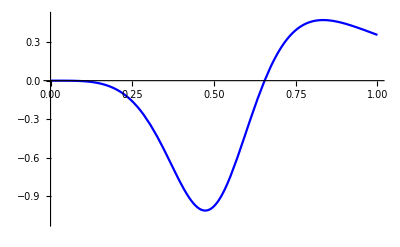

```mathematica
OmegaprimeprimePlot=Plot[OmegaprimeprimeCG,{a,0,1},PlotStyle->Blue, PlotRange->{{0,1},{-1.1,0.5}}]
```

```mathematica
OmegaprimeprimeEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,6}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotRange->{{0,1},{-1.1,0.5}}, PlotLabel->"Omega''(a)"
]
```

342 lines of corrupt data deleted.

123 lines of corrupt data deleted.

265 lines of corrupt data deleted.

6191 lines of corrupt data deleted.

```mathematica
Show[OmegaprimeprimeEFTCAMBPlot,OmegaprimeprimePlot]
```

737 lines of corrupt data deleted.

6481 lines of corrupt data deleted.

```mathematica
Omegaprimeprimeprime = -1/s^3 4 (-1)^(-p (1+1/s)) Subscript[c, 4] p (1+s) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-3+(2 p (1+s))/s) φ'[a]^(-3+(2 p (1+s))/s) (ℋ[a]^3 (2 (s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ''[a]^3+3 s (-s+2 p (1+s)) φ'[a] φ''[a] φ'''[a]+s^2 φ'[a]^2 φ''''[a])+2 (s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ'[a]^3 ℋ'[a]^3+3 (-s+2 p (1+s)) ℋ[a] φ'[a]^2 ℋ'[a] (2 p (1+s) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a])+ℋ[a]^2 φ'[a] (6 p (1+s) (-s+2 p (1+s)) φ''[a]^2 ℋ'[a]+6 p s (1+s) φ'[a] φ''[a] ℋ''[a]+s φ'[a] (6 p (1+s) φ'''[a] ℋ'[a]+s φ'[a] Derivative[3][ℋ][a])));
```

```mathematica
OmegaprimeprimeprimeCG = Omegaprimeprimeprime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

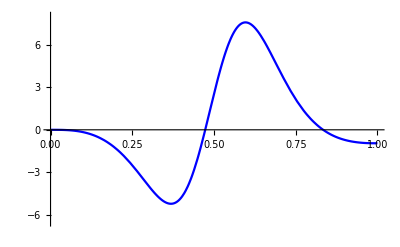

```mathematica
OmegaprimeprimeprimePlot=Plot[OmegaprimeprimeprimeCG,{a,0,1},PlotStyle->Blue, PlotRange->{{0,1},{-6.5,8}}]
```

```mathematica
OmegaprimeprimeprimeEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,7}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotRange->{{0,1},{-6.5,8}}, PlotLabel->"Omega'''(a)"
]
```

216 lines of corrupt data deleted.

227 lines of corrupt data deleted.

284 lines of corrupt data deleted.

6228 lines of corrupt data deleted.

```mathematica
Show[OmegaprimeprimeprimeEFTCAMBPlot,OmegaprimeprimeprimePlot]
```

736 lines of corrupt data deleted.

6545 lines of corrupt data deleted.

#### Lambda

```mathematica
LEFT=1/(s^2 φ'[a]^6)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) ((-1)^(1+p+p/s) ⅈ^(p/s) a^2 Subscript[c, 2] Subscript[H, DS]^2 s^2 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(6+2 p)-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(5+p (2+1/s)) φ''[a]+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) φ'[a]^((2 p (1+s))/s) (Subscript[c, 4] p s (1+s) φ'[a]^6+a^2 Subscript[c, 4] p (1+s) (-s+2 p (1+s)) φ'[a]^4 φ''[a]^2+a φ'[a]^5 (4 Subscript[c, 4] p^2 (1+s)^2 φ''[a]+a Subscript[c, 4] p s (1+s) φ'''[a]))-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(6+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 Subscript[c, 4] p^2 (1+s)^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(6+(2 p (1+s))/s) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(5+(2 p (1+s))/s) (a Subscript[c, 4] p (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (2 Subscript[c, 4] p (1+s) (s+2 p (1+s)) ℋ'[a]+a Subscript[c, 4] p s (1+s) ℋ''[a])))
```

1/(s^2 PhiPrime[a]^6)(-1)^(-p (2+1/s)) ⅈ^(-p/s) XDS^(-p (2+3/(2 s))) ((-1)^(1+p+p/s) ⅈ^(p/s) a^2 c2 Hds^2 s^2 XDS^(p+(3 p)/(2 s)) Hconf[a]^(2 p) PhiPrime[a]^(6+2 p)-√2 a^2 c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(1+p (2+1/s)) PhiPrime[a]^(5+p (2+1/s)) PhiPrimePrime[a]+4 (-1)^p ⅈ^(p/s) XDS^(p+p/(2 s)) Hconf[a]^(2 (1+p+p/s)) PhiPrime[a]^((2 p (1+s))/s) (c4 p s (1+s) PhiPrime[a]^6+a^2 c4 p (1+s) (-s+2 p (1+s)) PhiPrime[a]^4 PhiPrimePrime[a]^2+a PhiPrime[a]^5 (4 c4 p^2 (1+s)^2 PhiPrimePrime[a]+a c4 p s (1+s) PhiPrimePrimePrime[a]))-√2 a^2 c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(p (2+1/s)) PhiPrime[a]^(6+p (2+1/s)) Hconf'[a]+8 (-1)^p ⅈ^(p/s) a^2 c4 p^2 (1+s)^2 XDS^(p+p/(2 s)) Hconf[a]^((2 p (1+s))/s) PhiPrime[a]^(6+(2 p (1+s))/s) Hconf'[a]^2+4 (-1)^p ⅈ^(p/s) a XDS^(p+p/(2 s)) Hconf[a]^(1+(2 p (1+s))/s) PhiPrime[a]^(5+(2 p (1+s))/s) (a c4 p (1+s) (s+4 p (1+s)) PhiPrimePrime[a] Hconf'[a]+PhiPrime[a] (2 c4 p (1+s) (s+2 p (1+s)) Hconf'[a]+a c4 p s (1+s) Hconf''[a])))

```mathematica
LCGeft=LEFT/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify
```

274 lines of corrupt data deleted.

5 lines of corrupt data deleted.

```mathematica
4.367572272413816*^20 a^2
```

```mathematica
+
```

```mathematica
1.43857713640625*^22 a^8
```

```mathematica
, 
           RowBox[{"2.385022401318125`*^15", " ", "a"}], "+", 
           RowBox[{"114122.79839278391`", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}]]}]]}], ")"}]}], "+",     RowBox[{
     RowBox[{"(", 
      RowBox[{
       RowBox[{"(", 
        RowBox[{"0.`", "\[VeryThinSpace]", "+", 
         RowBox[{"2.908614427687602`*^16", " ", "\[ImaginaryI]"}]}], ")"}], 
       " ", 
       RowBox[{"(", 
        RowBox[{
         RowBox[{"-", "8.038109537485393`*^18"}], "-", 
         RowBox[{"4.984395699105951`*^25", " ", 
          SuperscriptBox["a", "2"]}], "+", 
         RowBox[{"3.2834889702111774`*^27", " ", 
          SuperscriptBox["a", "8"]}], "-", 
         RowBox[{"1.354497363752`*^12", " ", 
          SqrtBox[
           RowBox[{"3.5216931457552`*^13", "+", 
            RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
            RowBox[{"4.367572272413816`*^20", " ", 
             SuperscriptBox["a", "2"]}], "+", 
            RowBox[{"1.43857713640625`*^22", " ", 
             SuperscriptBox["a", "8"]}]}]]}], "+", 
         RowBox[{"a", " ", 
          RowBox[{"(", 
           RowBox[{
            RowBox[{"-", "4.246092718419266`*^22"}], "-", 
            RowBox[{"2.385022401318125`*^15", " ", 
             SqrtBox[
              RowBox[{"3.5216931457552`*^13", "+", 
               RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
               RowBox[{"4.367572272413816`*^20", " ", 
                SuperscriptBox["a", "2"]}], "+", 
               RowBox[{"1.43857713640625`*^22", " ", 
                SuperscriptBox["a", "8"]}]}]]}]}], ")"}]}]}], ")"}], " ", 
       SqrtBox[
        RowBox[{"-", 
         FractionBox[
          RowBox[{"1.`", " ", 
           SuperscriptBox["a", "4"], " ", 
           SuperscriptBox["H0", "2"], " ", 
           SuperscriptBox["M", "2"]}], 
          RowBox[{"6.77248681876`*^11", "+", 
           RowBox[{"2.385022401318125`*^15", " ", "a"}], "+", 
           RowBox[{"114122.79839278391`", " ", 
            SqrtBox[
             RowBox[{"3.5216931457552`*^13", "+", 
              RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
              RowBox[{"4.367572272413816`*^20", " ", 
               SuperscriptBox["a", "2"]}], "+", 
              RowBox[{"1.43857713640625`*^22", " ", 
               SuperscriptBox["a", "8"]}]}]]}]}]]}]]}], ")"}], "/", 
     RowBox[{"(", 
      RowBox[{
       SqrtBox[
        RowBox[{"3.5216931457552`*^13", "+", 
         RowBox[{"2.48042329737085`*^17", " ", "a"}], "+", 
         RowBox[{"4.367572272413816`*^20", " ",
```

36 lines of corrupt data deleted.

38 lines of corrupt data deleted.

14 lines of corrupt data deleted.

20 lines of corrupt data deleted.

16 lines of corrupt data deleted.

8 lines of corrupt data deleted.

11 lines of corrupt data deleted.

21 lines of corrupt data deleted.

5 lines of corrupt data deleted.

8 lines of corrupt data deleted.

51 lines of corrupt data deleted.

211 lines of corrupt data deleted.

13 lines of corrupt data deleted.

262 lines of corrupt data deleted.

41 lines of corrupt data deleted.

226 lines of corrupt data deleted.

```mathematica
KGTqS6XlLlbYSIR7YseyfF0cR9
```

IZ

/6ooByuuJtZa81g8JtQ3otLFblSSrKxbR/zKfIQ/2asiuR3V0hb95thieHs
K7UYVUQ3nf6f7L9mwCma7T7Gq6L6Z7eG3xO1AN3lqLH5b6oovPiw9S5ZC1CT
zNy7cEkNGUVWZ61Rt4DtKfe3okpqiNfZ8KEfXQswBhT8UfZRQ4RaxOanmVrg
0CmIWK1MDU2JtMqls7WA8tfGPWxMDdXRW7Kz8LSA0uCr6SuE6ijsH8XZJqEW
CC7I6dwUUEeGS8/WpSVbQML/fVGzuTriGXAaeSvTAr+WZHKtE9VRb+31dmOl
FniuLN9M/FwdZSaPZH/TaIFMFbSV9UMdOfsEB/jotgCxK4kVA4MGumnCa3HK
pAXyX/7ESm9pIFqZWfkUixZQ0DvS+BSqgX5cj+Fgsm+B/ivfOk7hNFAPqThZ
vUsLrC0+jaZf00AZ68sbUt4tILqr+vbK1VvIaTR1dMC/Bdb5r8dR6dxCsh2y
OIPQFpg20hnfjriFJnJ/5yxHtYDMLceW3s5bqCa4MtAzsQXKTcUEQ9ZvoWAb
fcsTGS2g7aB+l/fabaSnekoxMa8FYtWlZAb1biNOvuYbjCXHfL6mf9WNvo0I
LpiT11S1wBOadZOhp7fR+D75lnhjCxwpZNeIbt5G1Z+ejL1ub4EWd5/N11Sa
KKjXoUP32fF52D4jdOTSRLoVtHkLL1oARNXTTylootWYD0Fugy3w17ShOsNU
E3W5BlodfWiBvXxaWZ8HmihNl1spbrIFLo6MbnBnaiIHiWlO+s8tcAZHe326
RRNJX4k6V7nUArorxEsBHzTReULRbZG1Fuh0PSF66T9N9G1lcfzFVgs8biJj
qiLVQs/fJuO19lugONixkp9NC6U2Qf6XoxZQvy89Xn9TC9ln/Bd8j6gVGPlr
a1nMtNBfv3LrP2dbIUdhUjjRXwuNmOoqR1O3grz2oudWphaqkDvJTUvXChaB
OFfVVi0UwNFIUXa1FTys7/PmfNBC2uSmO4JsrfCE+0

```mathematica
boNfktps2qjYaf2D2elWgFNnV56QBZbVRRSBPqKNMK
```

23 lines of corrupt data deleted.

227 lines of corrupt data deleted.

171 lines of corrupt data deleted.

6220 lines of corrupt data deleted.

```mathematica
Show[LambdaEFTCAMBPlot,LambdaMyPlot]
```

737 lines of corrupt data deleted.

6416 lines of corrupt data deleted.

1323 lines of corrupt data deleted.

323 lines of corrupt data deleted.

```mathematica
LambdadotCG=Lambdadot/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
LambdadotCG/.√(-H0^2 M^2)-> ⅈ √(H0^2 M^2)/.√(H0^2 M^2)->-ⅈ √(-H0^2 M^2)//Simplify
%/.√(-H0^4 M^4)->ⅈ H0^2 M^2
a=.
```

1

((0.+0.186672 ⅈ) H0 √(-H0^4 M^4))/M^2

(-0.186672+0. ⅈ) H0^3

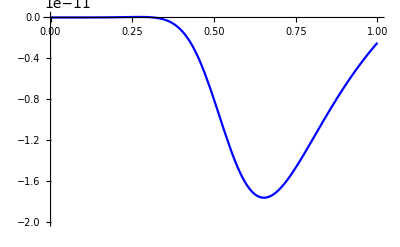

```mathematica
LambdadotCG/.√(-H0^2 M^2)-> ⅈ √(H0^2 M^2)/.√(H0^2 M^2)->-ⅈ √(-H0^2 M^2)//Simplify;
%/.M->1/.H0-> 70.9/(2.99792458*10^5);

plotLambdadot=Plot[%,{a,0,1}, PlotStyle->Blue,PlotRange->{{0,1},{-2*10^(-11),10^(-13)}} ]
```

```mathematica
LambdaEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,11}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-2*10^(-11),10^(-13)}} ,PlotLabel->"LambdaDot(a)"
]
```

495 lines of corrupt data deleted.

55 lines of corrupt data deleted.

180 lines of corrupt data deleted.

6214 lines of corrupt data deleted.

```mathematica
Show[LambdaEFTCAMBPlot,plotLambdadot]
```

738 lines of corrupt data deleted.

6376 lines of corrupt data deleted.

c(a)

```mathematica
c=1/(2 s^2 φ'[a]^2)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-2 a^2 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 p s^2 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(2+2 p)+√2 a Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(1+p (2+1/s)) (3 φ'[a]-a φ''[a])-4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) ((-28 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+6 p (1+s))) φ'[a]^(2 (1+p+p/s))-a^2 Subscript[c, 4] p (1+s) (-s+2 p (1+s)) φ'[a]^((2 p (1+s))/s) φ''[a]^2-a p (1+s) φ'[a]^(1+(2 p (1+s))/s) ((-3 Subscript[c, 4] s-8 Subscript[c, 5] s+4 Subscript[c, 4] p (1+s)) φ''[a]+a Subscript[c, 4] s φ'''[a]))-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(2+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 Subscript[c, 4] p^2 (1+s)^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) (a Subscript[c, 4] p (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] ((-4 Subscript[c, 5] s (s+2 p (1+s))+Subscript[c, 4] p (1+s) (-s+4 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s (1+s) ℋ''[a])))
```

1/(2 s^2 PhiPrime[a]^2)(-1)^(-p (2+1/s)) ⅈ^(-p/s) XDS^(-p (2+3/(2 s))) (-2 a^2 c2 ⅇ^((ⅈ p π (3+2 s))/(2 s)) Hds^2 p s^2 XDS^(p+(3 p)/(2 s)) Hconf[a]^(2 p) PhiPrime[a]^(2+2 p)+√2 a c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(1+p (2+1/s)) PhiPrime[a]^(1+p (2+1/s)) (3 PhiPrime[a]-a PhiPrimePrime[a])-4 (-1)^p ⅈ^(p/s) XDS^(p+p/(2 s)) Hconf[a]^(2 (1+p+p/s)) (c4 p (1+s) (-s+6 p (1+s)) PhiPrime[a]^(2 (1+p+p/s))-a^2 c4 p (1+s) (-s+2 p (1+s)) PhiPrime[a]^((2 p (1+s))/s) PhiPrimePrime[a]^2-a p (1+s) PhiPrime[a]^(1+(2 p (1+s))/s) ((-3 c4 s+4 c4 p (1+s)) PhiPrimePrime[a]+a c4 s PhiPrimePrimePrime[a]))-√2 a^2 c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(p (2+1/s)) PhiPrime[a]^(2+p (2+1/s)) Hconf'[a]+8 (-1)^p ⅈ^(p/s) a^2 c4 p^2 (1+s)^2 XDS^(p+p/(2 s)) Hconf[a]^((2 p (1+s))/s) PhiPrime[a]^(2 (1+p+p/s)) Hconf'[a]^2+4 (-1)^p ⅈ^(p/s) a XDS^(p+p/(2 s)) Hconf[a]^(1+(2 p (1+s))/s) PhiPrime[a]^(1+(2 p (1+s))/s) (a c4 p (1+s) (s+4 p (1+s)) PhiPrimePrime[a] Hconf'[a]+PhiPrime[a] (c4 p (1+s) (-s+4 p (1+s)) Hconf'[a]+a c4 p s (1+s) Hconf''[a])))

```mathematica
cCG=c/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
cCG/.H0^2 M^2->1/.H0-> 70.9/(2.99792458 10^5);
plotc=Plot[%,{a,0,1}, PlotStyle->Blue]
```

212 lines of corrupt data deleted.

], 
     Scaled[0.05]}},
  Ticks->{Automatic, Automatic}]], "Output",
 CellChangeTimes->{
  3.7644886761722307`*^9, {3.7644887697843246`*^9, 3.764488775295207*^9}, {
   3.76448934796

7 lines of corrupt data deleted.

32 lines of corrupt data deleted.

327 lines of corrupt data deleted.

CvDQ+yLCa0KFi7MnJv+Vcen4/Nc
b3ghLceFXSX5YnCnHg+hFiwP8iy5MLqlp7ILrXhIXSwTZwnmwuY62XjtuvAg
vk45bFfJhVWVtJIQD+KBaInHom2KCwuMsl8MGseDz9zABD3lGezBG/5vXDN4
MCYLVflP4gwmY9pbmLuIB/3qB1luBmewLkW/sKtreBhiFiTLcj+DpYrKOLTu
HPcnHycfX3AGc6RdMNQ7Or5/1oGxjPEz2I2tMJglroC037ThvSe4Mb6Ra3w2
lBWwf+Uuqzo7N7Zbs0ZKQF8BI8OXXWoucmOdyfFLH1gqoIn+V7OICjeW4qXR
yc5VAX6bRTuBRtyYw9P9oiz+CmBipaBfe8mNaWplhkudrYCpOllWNT9ubFrS
xLHpYgXQ9lozxCdxY3hW2ns60hXQU05C8BvPjX34Wy03JVsBWQXqc5c6uTHT
mcf8VooVUJpo3GQ3y41JtZ4mP1KvAIE/2SlF+9wYVV7zL1/tCmCNVPFYoOPB
poJfdp2+UwF0tV4PWYR4sHJ73pL0+xUw6hGvI4/xYP6G3RGSFhVwfatezVyH
BzORc3ld/7QCuPjO3vR4xIPt8EkZ3bStAI+tLYuPb3mwDvI5+QnHCpB/rReS
F86DJS6HCDx1rQDB5ncDlTk8mF2vHMX++wooyWD252vgwdTxK7+9PlTAR5U4
7okxHow7NrabOawCovIRR8gWD7btqlaaElMB4qzX3IGaF2s33428mFQBf25e
15sX4MUS1NKdvmRUQBDX6Mf3srzYy/O69zXzK+B1nZYetz4vRslIrTBWWgE3
ia75lFjxYj/+VAk++lQByjfopeW8ebHScUvKP3UVoCona9GcyIv51J1a8Wyt
AGSrzKJUyYsZpTf2MHRVQIqg040vPbzYJT+bssSBCrDY1qeVWOLFKKy5o8XH
K4D0zLl78UR82IRup3P1dAVwPw3AnWDnw0pknI3VFivgMse3PLNLfJg3l+j1
4dUKaHl+BV+tzodxEs0IWexUwOe/Koa0D/iwjfmgk1uHFbD4/WqcoTMf1toh
u+pGXAnOjjauSWF8WFzh715aykrIldUjn8rlw2zCY8rj6Crh8KmkNFsTH6b8
WiXmLEslLCsYMmp+58M47u+8qeSshHVK59MHO3zYukKqiTJ/JRhfml3iYuDH
WoS1FQdEK+FFwEo2Towfi6UmEDG7WAlCcqZ3tVT4sYvrFVTrUpXQLbtCZGzG
j5EOWqy5yFbCLQH65Icu/NhYFVM/lWIl4FlCMMtofqwwoR4fo14JoRNkIyal
/Nh7T+uPwtqVcMWax0G3ix8zfMT1tvx2JWDhdlxyS/zYhRtfTa/fr4TAn+5d
/CQCGMml10q95pVwPoAukIhbABtlERY1floJWpuexiNXBbCCwwHqFZtK2MVl
KGfdEsAUJwPWnRwrIT2jSdnGWgBja0IDFK6VcNcg44GknwC2mrVUEfm+Ev6r
K05aTRPAGgOiYgU+VEJXbwRRaq0AFm2r5FoSeozvTPLVGhPAxPX/mcnHVEKY
82Nsd1sAI0Z5yl2JlUCX7sUVRSeIjXAbnr2XUQmkFfcvXjwriOWTUND+yqsE
I80Xjg2KgpjHUvmGQ2klEBLi9m8YC2K3ux4Mkn6qhKu4Xlh+I4iJlTJUhdVV
QpNrKhR/FMSIo2vjeFsrwWmBNM+qUhAbfvPcrbDzeH9lzU9gSBDLM+Uwlx2o
hLQqkcm+LUHMXbld5etYJXBYOeS9ZhDC9M85nDOYPubr1/+H9YIQdo5ekO7n
z0rIGO6vL9IUwoh2+jbtVivh84A1w7UnQtjQqNsQ8U4lCDvqL7V7C2G5X85/
Cj6shJ/z/93QSBfC3FK/x58hroK/13iuNTcIYXo+fu55FFXwrCikTXpKCDv7
XMYCR1cFnsI6P1P+CmGEOguqbaeqQPGrSDIZhzA2KBUups9ZBf9CmvbNZISx
HA4F+jm+47XNwHaFnjDmSri+ZSNaBRGm5JGkL4WxW/PxwwQXq4DhNvW0RrAw
JtqhUR0gVQV1qqGjfvnCGEHhfgKHbBWkG5p4NnQIYwNhmR7Z16tge//79OZP
YSzbUe+htHoVmDv+3OMgFcHeGp1Qb9aqgvEX/77K8olgugrF4rq3j+NPizRq
KIhgosLGDNNGVWBMt93zx0wE+0dFs2NlXgVTkhL/Y+E6w7l+v7BSGRWFkAZR
ZO8RjmPvvffee5SIpKGMbFFKkUpJRX4h87uHWaKQhkrbSBpE/b8v/i/P9Zzn
nPu+z32e6/q8+ZAqT0nDyLeO8dUoFh/V+fPq16Xh1tOIrrzEdjT04fFkUKUh
o0OoZnsqq17+f1xO76XBqZp6qu5YOz43mrg9ukEGpLOSwtVPt2PZY19jeykZ
+Buxx5p8th2vbo18RjKTgSe2Q4oOpe3IsZ8cLh8uAzdVj/K/utCOMmUBK4XZ
MnBUWPZXdHU77md3Kf98UwYcV8cmlm+04wNaujYwZWD/m9Pd2XfaMVup7euZ
TzKwSlO7KvhfO7qUvG/s5ZKF4dtvsq61t2NW1L/c9TKyUFdUFKFCbMeBzW8y
tCxlIf2Qng2B3o5vemOKgiJlwcHzq5LtYDseWTxOPp0rC1JYKTA50o7vMgd2
XK2XhRUJ898Rz9tRe5d/1YNeWXjM+fP5rylWvZ6PVsTPsnBjprYn62M7OrSb
ylK55SBt2KGWf64dGUoGSJSRA/vWf6drfrRjxvNwc1krOZC8dCdScaUd64L3
K3LGycGfTC/brrUdWGotETBZIgePQrhUrLg60F8/4k1dixxct2zdNs7bgQbJ
jq2RE3JwRDFkKVSwAzmYG97t/cuqL8D/YnFnBx7jvxv9dI887FsiEE5IdKC8
b7bLMRN5SH08eW2LTAe+Otl1VTRCHmxbcrMvK3XgfWUf99az8rD3ola0nGYH
JhkWHjFtlIelY+/t2qEDb3SXbh54Ig+DwWWq5sYd2LwvcJvVL3motTAUemrZ
gTsztcsJIgqQojC/HOTQgRY2AmXyegpgw3/55Te3DuQOF+IvCVAAid9WpGO+
HZh21Elo9pQC/J5cur45pANbtceuGdxUgAFiXc7FqA6UFK3qOdunAFdvuMRI
J3bghfW9UUOzCnA4j92hNaUDk2Nc73DxKYJNfJOaybEOfM7umK2jrgjiLn7C
T7I6MF3kEluIuyL8OrB5xf9sB+4/6y1yOk0R+nd3vJot6cCy+sTxy5cVoYY9
gpx+oQNfiM8a3CMqQvJHwTru6g6cZo5q639UBOsBSu75Gyy9/8g9onMowZ77
ibGSdzrw3ujjicgdSvCzXMzxv+YOdC3MQi5FJehLG1Q3bO9AOc9MtlpDJaj2
T9/+iNCB8dpvRLVcleCQicyqD70DF1LmrjAilMBKZuz1lwFWvJ1xwvmoEojx
nqakjnRgsN213udFSvDju+pNjucdmLfrWqrvNSXoHZvKOzfVgZlXvhdPtirB
la7COImPHeg7373NtU8JDl4Fp6bZDgwTkOToe6kElme+aOCPDiyEgHCdBSUQ
jb4gMvCnA4MMU3Tq1ivDor3ZX8+1nfgPKk7wbFcGpvqPqY+cnZhh9RkT5JTh
skgtNZm3E03csw4NoTIk/bO/tU6wE8+HZ++TdlIGi3d/z5bs7MTWTH7HjFBl
2M1siBeT6ESuAu3VwVRl+H7H0/mudCf+OrpVeke+MjBKOLV0lTqxMoryLLBa
GaoOt+zo1ejE4/JeG280s+p7B/9zg048UPmC+o6mDOYGfG+njTrxZf9hLtEJ
ZdglSaAlWXbiuwuXXI/OKcMCd2z9GodO3D1/7y73ehWgz+0oKHTrRMVqW+5S
ERW4NMJM2OXbiR8WOqMElVQg8eFhl9vBnThjZjVaZqICZpf3HTgQ1Ym8H8GC
x0sFdp58spOe0Ik7do4zT8SrwLew42wuKZ1Y6pnqsZClAjRrxXdvMjqxqNty
2fuiClxUfkGPz+rEc9237pIaVSBBMO/23zxWfHYwRYKmAqZ/tArPlnTiac9v
nseeq8CO1+8TRS50Ik92oNvTeRWYp5S53rzSieJmnvH7N6gC9ZahtsaNTix+
vfPmoR2qUFkwv4vSwNLLvZetW0kV4pMur3Fs7kTivp70NaaqYOJuPf3qIYt/
kNRufS9VEIFlRgyhEwdkFT+kxqvC3J6bDX9onUhu4pm4m6UKlA2uRTkDnbgo
+ff3y0pW/S/sB4VGOtGpS92Uu1EV4h41uV2f6MTVwimyElUVjB/46ahOdeLG
dvmDjhOqsL1ysyjxQycmxTh6xM2pwmxGx1q72U68WBF06Mw6NSAHRbyfXOzE
Tdc8LCtF1OCCuVBv5J9ODF4TNQsqahArT73ze00Xzj8p0J60UAMjvqTi05xd
qFyyR/lQgBoI/xI7JMDbhaeYeSOcqWow83zQ/eq2LjTk0JCqKFIDEiFdV2ln
F16ZK5MVu6kG56/LiHWLd2FU39e3tT1qEJM7xm4t3YXNLt2O4s/UwDDu9Idx
xS4UnfU4cnFWDYSc1frCNLpQaeNOH94N6vBV683dH7pdGCYRsHp0lzoQdxWV
nDTqQjFKsc8HNXWoWKuXvNWyC9fY/D1mZa0O0R++eFyx78Kzauxh9UHqYNB/
AeTdujBiYl5gXZo6CDaZ7enw6UK8LHTWvUQdvpz7sc4iuAsjN78erLulDoQj
tR+fRnbhC48Tr74R1KHcz6E/OKELF7eEETTG1CHK+N+9hcNdeDWYlpQ8pw76
0ndKMzNY9/tW/jRu0IBtPF6HebK6cOGap9f7XRrweYHT61Iei4+EcJmgugYQ
nrXoyZR04bXO4psG1hpwrjNYvO18FxrV/qsMC9KAyBq+DaZXunBC9EZM9hEN
wNOET0+ud+EoXVvIuEQDBKJiBwIaujBb40mWfIMGfLLb2TR3vwvNg5/obKVp
QI9ab9nRh1347MCIztwrDeDf/D5lI6ELjRNds+lLGvDxW6n3BVoXkpoGJSr5
NaHrqYG+1EAXBjR3bQmT14TSjjmJB0+6cMqv00HBTBPCq6s4jCa6kCwv9WnO
XxMgy+rLo9dd2Lu+Yvz2EU3gi1wa9P3QhXaHDu4LLNOED7Z197/OsPCJqQ3x
3WXVV3UpP7LYhd7jgeNddE0oEWY/wvmnCyXlI0yDpjQhbLXRp3xNN4oQOoTZ
/2iC7htfg72c3RirMeRYJaAFW+mb9t3n6UYXNeFfygpa8P52O6f+tm50UPrO
QTTTgs6i8K8DO7rRcuXrGcsALSg+JPjIS7wb3/9ySR08ogWhnpTmT/u70Zt+
9aV1mRboYGLFYcVuXP9bp516Rwu27BVLW6/RjbpCuTwH6FowzTnoW6rbjT73
f7y48VoLOmbSDPcYdSPJ9YMM77IWFA1LS96z6Eb+4Hu/EvgPQEjrMy6w78ZT
GSTTIbkDoH0pa6bXtRu71yeISJkeAN7jqo/dfbrx155ysTb/A/AuZOq/90Hd
eFya/YTI0QPQbll4/mBkN5Y7zFGSLxyAQkVIX5vQjfWNG7/2PzgAwQJf/IoO
d+N14emlncMH4MDSeaPdGd34tEXrW+jsAeB5aSrVcIrF3/TMSD23NrwlLXJr
53VjFe3QjY+S2vCw7uosvbgbIzRvRYgZaUPBWfthl/PdWBF5V8zRTxuCEv4+
eHu5Gz+Y7x48mqYNWq4NFxKud+OPx1UHayu0YbOO59F/t1nxrRpBcjOrvihn
QP59lj4fJlomh7ShbV2L8Y6H3ein0O02/0Ub8j8F7b/V043nM+b/rHLoQODg
1k2atG6cu/X3+vq9OqDZ3DNH6WedO/u4c+jrwKbzMU8cn3SjUkbTNnZvHXiT
vqP19Xg3fuqNe/37sA60BjArY19342kJ5Y6PpTpw1vRwxsr7btSRi7w5fE8H
AmT3BebOdKNg9cX6lj4d0NjyxER4sRvHw3wpZR90YOOPTOkby934csuO39Hs
ujA1rrBZbU0Pbo7xNUdRXWjpnpwncvSgne2D1o06upBXmztix9OD5e/dzIdd
dcE/W6vthUAPEuqkVksSdUE95v3FqB09qPtaMSW4WBe4HcuOLe3pwQOtCz3J
jbrwWsMw6Mz+HuzQE8k4MaQLD3bMm25T7EGjmbUPzszqQi7bZZla9R4c3nUi
7PRmAL9pKx5l3R6Mko05nyEHoNa79K3bsAcLz4pZxlsBcN+rG7W26MHuzM/H
vCIBXpW6PJyw68G0DCld/RyA/1LYq8Jde9BsRfX47psAOT5NmT+9e3Dv7meO
P2kAvoZ+waeCerCkOO0+fRpAVWqzOV9kD5Yd+Vhbsk4PuDZ1yFbH96BM1Bpp
Nwk9eDkfzqtwuAdduy8abzPUg+ZRwe8dR3uwsnn9cr+/HmS3U55anOrBX5Pi
VhnH9MDnSmL7s9wejD3H0Ja+rAcqp8QuhxT34Bqt/r6BTj3gjBg8/r2iB5tE
2ddEP9eDFzbpIccv92DmS/tJ9mU9uK8iY8F7vQfjzqcHnBNGOCM0Jld1uwf/
Lc8Xi2kieK9kbZG934P3TVbir7sgKE+pLra19WDOk6Q1ew8icNCmnpn29OBp
DR2TSyUIk/WFHSPUHqxnSiFPE0JTIVwJ7O/Bnx94FlKHEE4f/HJifrgHo79S
/V/NIHh5XAjNGO/BrQ9Wd2Vw6IOSnpnlptc92PItdHemsD5skPghX/m+B7ss
G69kSOvDc47arftnevDTq8zaVG19aPxq/+PB9x5cfnRMNsFKH7Ie/x0zWu5B
ZY/nWiHe+iDv5foynI2Ag83EfpcYfThvI//oHjsBhxMFPxlm6MNa/XWknxsI
eOwxR6FcoT7EqDxvBm4CuhxlI/BV68PY3vvXT20m4IhE1NEfjfpgKJRT0beF
gEcT7zNGiPpwh8s/h0+AVU/QoLZxWB+EVjTSPIQI6Nh9nCfnrT6cmN0cUy3C
qi/4aqPvoj58ff3O98MuAk70ky8prjcAtycd9gp7CPimoJK0us0ASNQSw0N7
CTheUZzBkDQAubYItU4pAuqf4x8u1DQA12uHJdllCfjsBr3bydwAiOW2wpYK
BHzFMWki4MHKz9nHXazMuh/SEf44wgDK01b+PFMjoEnso/15RwxgTeyTmd1a
BAzxtjhjkGcAUf71r0J0CNj2oihr8aIBPHU8/rhBj4BsfLb7rjUYgIGJO/m7
AQEz1O6F2XcZwG1NxQfaJgRMzHxjszRgAIIyG+qOmxPQu9Zx/PJLA8jc+eI8
w4qAfztvbDSYM4AvPP/l8toRMNVsQ/WVNYbguiYv3dWRgD/MrjtoCxgC4XtA
bJULAdX0D5g9ljQE2fda/u/cCfjLLuJE8AFDODfG6yjrTcCevdXrFq0Mga3v
vVGiHwGtX54aOuZrCJFdXeoPAwkoKnPiHUeCIYzeK5NiCyVg+4O1JmdPGoL+
1ajtZhEEnKy+s7Cp3BDqyww3FkQTkC7ZNJtz0xC2ndm+OhJHQJ2w/7TZOwzh
WOr87I4k1n1e8bGUAUP4HEV/HZhMQHb9GsbnV4bg4nt5+FYqAd1V/Td7LBhC
j/0hynw6AY9wbbhJXmcEMkbWLZqZBPwUt3pBRsgIytQlbmacJKCkQNO7fGkj
+Ce1fIF6moD3a/NyZnSMIFLkcd6mXALa6KnlWtgawcimm0ed8gm41HDpQ42/
EeC/jLjKIgL+/P6u9meiEdz65hIwVcqa5+TfHrMsIxB4J+e0v4KAdVnFcK7C
CDKespvEVRLQS7Zv16tbRvCJMaHRUsWat19h4L5OI3DuaNq/Wk1A8uehTeGD
RtB9J1vE+BoBNWZUd9e9NgLpar9NeXUENBCQPP9mwQhKSzT+Pq4noPjFkTSR
9cbw99TmeeG7BLxY877XVsgYIg6/m/JrIuD094/Xd8sYw5OIjic3/iOg86vo
vsN6xqDnXUKdaSXgXomM7/2OxnDTNqJVrYO1T9FnRHeHGQO/gf6ttG6WPpOK
DlFpxnBUVegiicjaj6Lduf8VGsPHfbNnuagEbK5f7luqNQYnYWqGPYOAc8EL
QjptxtDFfSm+oo+A9q8a4lL6jWH/amLgy0ECjt3ePNr02hhK5iyc9w0T8HTp
BosPi8awOiVmGj1KwEuVrQPCXCYQPvJLs3mMgJ4rtsGmu0xgmDYovfycgMfH
knjilU0AHl7fYfCKgE9sBwbOmZhA3e30zdlvCFhYmVPb6mECfJed/g1OE/Dw
c7vi0RgTOFok823bJwJaKdPPzx03gQ8n1rz1/krAfAvPjvXlJuB4aGykdo6A
K0aNy0L1JtAZdo/2eYGAz71+uUl2m4CU5+k25Z8s/zQ+HVEaNoFia5/6lCUC
fgj8kaj53gRW9NQu9awQ0E20W1V72QTClDcWbGAjYuoeP+EDPKbwWOLNMRt2
IubH/BZXEzcFXcGHCWUbiOjiic6yGqZwg7Mo6DkXEfm+Ot3dbWkKW/+Euohv
JuI632AVHl9TSJ8Bs4gtRPw6JPRmKcEU3r8SONDIT0Tuo5e6p7JMwWH4i8wv
QSKKZV1gUi+YQgeFtFNPhIiGuq+zP98zBcnWCzxZu4jok2C9VpxmCkW34tn6
xYiYNLCs7TJpCn8umi3w7SWiWXyJ2qkFUwgt2P3OQ4qIIr6q3+5ymsGjzB+j
1TJE/OI3lDC62wx0kvrpH+SJ2Mlh2fZLzQyuh9Q+VFAmYsGH07RtVmawxf3I
7UNqRKzR/q9KMcAM0iwdqjo1idgqloomh81gWnd/IbsOER/JPrzjmm8G9or/
Mi31iBjL9epTUK0ZtO95mlhsQET78eIf0Q/NYJ/AneAxYyL+NtcdThgyg6IN
p1xFzYkY9pl4PHHaDJZ/e5qHWhFxV1T++rg/ZhDyRVn7ji0RL6Vw+YVtNYeh
F5xyiw5EfHdte5GXlDloP3q1S8eFiMlV+yutwByukVp4T7gT8QlvTYamkznw
Pshfw/Qi4p/8UBSNMIcjdcHfef2IqORU92LtMXN4d0Fn2jWQpd83U683ZeZg
d5bvWVUIEU9mf33YVW8ODzM+Md6FE7HWibZcRjCHvQmEdtloIpYkpomGPzWH
wqCKhsQ4IvKvb5bW/GoOSy6xlx8mEvFa2zORtWstQMIwvYgtmYicd4oWGUIW
UKDmdMIslYhsa7Pa8uQtYElS5mBBOhH7Ft6EWRpZQND2NaGjx4gYtbVg3XoP
CxjcOOa28yQRr7r4bv0bbwFaf+9aBJ0m4vsUyRuQYwG181k69TlE1M+5fj+l
xgJ43nrLfztLRBU1U617Dy0gZVRVVKuIxf/o/gNTjy3gLZ1767FSIr6sOdLC
89kCbNqn1tLKWf645n1fc60ltDW0LW6qJKKyygEFbxFLEL9S+N6piqV3VKts
uool5BeHjlVWE1H1bXtDhaUl/D4JvVO1RHzV+vn+3UBLCEwW6NxfR8TIiiYk
HrGEgfAvd+LqiVha0+I8VGIJml6kKy13iFg1sX1xrN4SrtpcKF5tJCLjKJfo
S5IlbNaPP2n8HxFH6uWevZywhMMqZofyWolI/h66+/mCJbzZuztsuJ21byl+
P4e5rcBa6If79m4ibnqf6U8Tt4JWrn5LfyIRPw7e9X2gbQXiK1d16yhElI0V
WrjiaAVnZ1MVZulEdNYW2nU60gp+vbYXU+8jYsjKlddhJ6wg4IkUX/ogEf1M
z+mZsBzVT/3LTn5MxLVal7V237cCjbbRH1yjRNzyLeDRAtMKauobPtiPEZFL
1IqDPGUFm6pOjlc8J+K9KbZXBUtWkFzo2ffyJRHX9IV6uG61hqnjyl373hDR
QPD24e3S1mB1kPNe9DQR412adMb0raEl9FV180ci8mq8u1Hibg17PFpKlr8Q
0VpO3zco3hryrPJPGcwRMchkcsOzXGv4CcHJ2QtE3K+fOGFy3Rr8lXTCh34Q
8eLd6Yl7PdbQJ87nKbhExKONL7i2TViD+rZPVj4r

```mathematica
A1/4R
0cn4zvIjHhvYuFyu+GUtCbmyeQlS0jZw6GvMHpUNJLxP2tiRamQDr18a86dy
kZBXwGKG5mMDlo93rCdsIuEentvuvCk28IC88HPDFhLefDT217HEBsRamB9t
+EkYlpY6VdxgA7k3qyfKBElYxXdnbT/NBn5UHu5/vp2EeY9rgtZM2YBfvm23
+C4SJnUe3qDyxwZ6j+1rjBAj4dPMC199ttmCeuJKTaMECf9r/CyUpWgLV4Kf
lP6SJOFgFF9unYUtcLvVZ+nJkHD6casxNcgWDlocP5wlT8Llg90WL4/awisd
94h+JVb+wYHKhQpbsFBQ9OJXI+GbDLsDa+/bwn9iG2w8NUmouW+/1OZ+WxDl
f6FXo03CgSXtUP73tpCz/j+lj0BCyfqFXwJsdrD4K1dc0YCE7K4/X2wVsQPf
zwECycYkDC6UFuFWswPmpNaGLjMSMtl/3Vm1sQO1Id7f7FYkTG7NuPg1zA4u
E99/srQlYUTS/bdPj9sB139dz4sdSLj37mx250U7SLpRNjDmTMIPVwPOVj2w
g5fno3pE3Un44O3sXOqQHZjnGTaFepEwKn9nw4nPdtB8dHvtHV8Srhi0zN9g
t4fd8fNliwEkXLe6Z5mLzx6yA+mndUJIeI9jX1KkmD18d76cciKchH9lmrwZ
CvbgY3YokhnFmm/E01YJsAfGAWvvLXEk1ve5ZVa6lT2oyknYuiWSsGftX+qw
hz1U7V7Gy4dI6Dv/9ohkuD1wbn2sPJ1CwpP
```

```mathematica
TtnDix8Z25KOkfAlud2Lr9QezD+6cLSfIKHG7LHPXjX2cH9CbontNIufz+i3
q/fsYdcA+xezHBKmC/QlfuiyhzM9E5MFZ1l8r6rFSvfbw0JT0+BoIavfI/bp
8Al78L6WTdhZSkJKmMzY9Y/2QC/3ux9UTsK5bh/z1z/tQSVH41r9BRKuv1Ko
IbzeAS6lbS7/domlz+OmWht+B+CIfXdGq5qEQ+8qijL3OECCf0fqsVoShtaq
/m1UdIBJx5Io2g3WPEeTZ16CA5iZRPhsrifh+Qu/fbmtHaBJU9/O+Q4JBWQ+
OKl6OsBOGSGDi40sfV/86vcId4DTO2dV3jST0DVjZ9/RZAf4xkPdK91KwskA
brsrpxzAa80lwfh2Ej4mz3l0lzgA7XsiZ2sXS49sk68T1Q4w/ypzeZXA6v/l
AMePu6z8YbevxhQSzqZX397UxcqnKLzMo5PwbYnCxJ4+B1BqXf9ouJeEt36O
lqqNO8DFW5PE7YMklFv1m+796ADrLzU3+z8moR/7SZ/43w4QX5B7vW6EhITP
Jjv5OR1hIjOgYvYZCW3SK8WbhRzBJEkrR/05Cfe3FyXYSzlCYwhvWvpLEjrG
iHB/0XAEEff30eQpEtbv2zhzwtQRsiy7fLmnWefTiTuEXR1hTrfM3uEjCaV1
95XXhziCp2KU4fkvJFT+zu+rfcgRqHsM1V7NkjBnk91B+ilHUBTYLim5QEJ+
4fpxhzJHqNwwLxTzg7W/LwULx2sdYd0Sjeu/3yTslD5zzrfZEeK+VP1Z/sPS
k/h15jWJhf/FwRmDfyw/a+644D/sCMaPrF5lryXj4Tzx8y+mHOEeSfzx0Hoy
Ltg+/eL2zRG2P1giCXKR8YTl/nNDbE5wqu7Rfz6byChlxn3OeIsTzF6ou3GN
l4ykEbuvLaJO4HE24/wXPjIm/eC8JKnoBJQMl1wVQTL++ff5WqmeEygkyKWn
bidjpeJezr82TnAhiD2WsJOMW55H0EJ8nIDddcKPQ4yMfn13XvdGO0GseZOD
```

QZQ4vIbvLpTjCunW10TpKMpnIdcvl5TmAk76c+KU1GtvDT/p8rneCuqIaU
hDwZnSonvhvXO4Ew3+btkUpkNDx768Olh05wct077iZVMvZtmNZdYDjBzM/2
lV8aZBy64L9oPOYE7p+KZ/W0yWjPw8N77oMTkJ+Hv84CMtrIv8p/89MJ5Adx
uF+fjE3nGQfdOJzhPEGQwm9MRs1f3D5Ows6wtnnmgacZGR1p0wHW0s4Qc51S
V2NJxn2cEacMtZ1hrOLihY82ZLyXdZqqbuUMhrmJeYoOZNxqYCsp6e0Md9It
jiY7k1Gut7SOP8YZhOLE4rrcyIjeWZZ/jzrDiYBf/uu8WOdnfvK+L3CGGadB
RytfMn7nH//de8UZ3EyvG5cEkPG/dbDhTqMzkLTSNcaDyZggLnDgLNEZ5GSd
9ouFk5FrVbkkfNgZKnbJiIRFkbFriMJn+NYZ1mxZs+luLBnzg7o7hBedIXrt
2OpiAhl1eEfyv65zgWeLd+d0DpFxA49abtc2FzD4kDV1IoWM8/sfNeVJukDD
uPcTZhoZf++vXO+m6QKC/arULcfI+K8q5LSouQsc7+ZudTtBRslcQ/Vpdxf4
2jh183IWGWNaxPlvRriAa21b5XQ2C//9cbHwIy5APFd4Vu4sGXcdP+y3L88F
ZLNDM5IKyUiX2PTo1UUXKD8C8e0lrHm3KSRVNLgAW4xA4JpyMoo3y1pad7lA
lN8XJ/MLZFyMbHP5O+ACTx1IJoWXyPh56l35nZcuoG98QfPpFTK+qzvF4znn
Arc14qV31ZLxbVZOFzubK2yTNtsRfIOM742nr9VvcYXMHbs3375FRt4PdVTb
Pa7wZfOPv98ayChKPi02r+wKLmz981qNZFR7XtxSYOgKhIWrb441k1G551K2
jJMryEynjtBayDgl29fDCHaFc8/saZvbyTj4eTuXwmFXYOuVanPuIuOOs4HG
RTmuENn599ZFAovvWHni3EVXGL07evENmYyjF26WWd11BaxpyJemk/EkN+32
NYIr1JeePBbfS8Yn31+3LQ+7gsBpz4TWATLSdn/ptJl2hWMpykF/H5ExPX+x
reqXK3yO5HQxGWHpwzl35zOXGzj7vDI9+4yF17P/ktpON+ixa9F6MkHGxM72
02kKbiBtmC8j8pKMbb9vR/fou0GZWvDOgCkyrhsrtmNzcoN/kjo8N9+R0UXC
V0kvxA0itvOxzX1g8ZsU25J62A1GNn76pv6F5a8Nn+cac9xA72/P2/RZMh5U
yn80fdENbs2Xj5K/kbHWW6RZ6K4b8L+NoXP/IKOI88nzpgQ3yBg1fujwm/We
CI8dTxx2g0/0HbfP/yGjyUHu+Ivv3MCpfeHSq79kXFbYFEz86QbdDcwCybUU
3M435PuO0x32X6nOjFlPQYpoUMC6He5QWnw48T9OCi6LtUfvkXeHrqNZwX82
UrDrJfW4DrLy471dDXkpKOdVXuPo4A4lgarmOXwUlJb81x8a5A6rztzaj7ZR
cMRgy/qUQ+4QbjYlK7Sdgpv1qixPn3GH4QNtu3x3UlDAdeRy8QV3ALlC3uui
FOzfnrO28rY71O0OXfNVnIL82wuTr3S5A99W+K4iSUFLhspKzZA7HGUXmE6V
piCfycaymil3+PDj81OCHAUbek3x8nd3cPxIZHAoUXCrouPdpg0e0Dlxvt1W
lYKxpnb2xSIeIDUQ13BOg4JOZVsexih4QEmP6eXJAxQUz3/zydTQA1aadhVJ
AAU7COff7nT1gLBri8cj9SnoGxlQNxfhAY/L+5KajCi4yUlBo+eoB+jmXA35
bUrB6XTe4rxiD7iRluqGlhSUlVB96HzdA7bG2luctqFg1SXbeyIPPSDdX0pn
wJ6CneX9B1/0e8B7x79yAs4UtAgP5K567QEOJqO7vdwoeMpaL8Fj0QM6NBu2
XPWkYL5JfD0fpydIypxc+8mHgqZv+1oYOzyheKfnomIABXkrqyrSFD3hD4/y
++RgCjKX2mxkjTwhdA3nWFcYBUvXKUw8c/WER99fMtdFUbCwc5Pe8UhP0Hn/
oMMqloXns+kRqQxPuD529k5JAgWh+Gthb7EnbOkLujJ+kIJbUueORV73hLQu
7WKxFAq6XfOz4njoCdP3tp4MS2PNY1Lhe3W/J9hf/XjwbgYFT3jlpWi+9oT2
sp7QH8cpeOa++WTvd0/Yd6bcXTeLpXe9u6gXhxcUpcZYnsymYHMLh9FHES9Y
jjLW7c2j4PMfX80SFbwgxHeHwtZCCu7YlqS4ZOAFQ/YLou4lrH4qysvpLl6g
bcTceuUcBfcQk26thnvBdfVq9vfnKSjjyKOXlu4FvPsP/5C7REHrD1se/ij0
giMith+SrlAw2yJmR0ytF7zbtG+8/SoF/x1RDZ1q8QK7f39619ygYNFGzUrH
Xi94+G240/wWBX1Wz7QRXnjB3ne37hY2sPxR+/hb8YIXFD7NrH56j3W+cuf+
Eoc3LDHcSnY1UzBBY5DXd5c3BHconApuoeBvkb3cPSreMHhnffLthxRUmX5x
dae5Nxyongxb6KSgmO/MRLKPN1wrafY4QKDgWmJm80CiN/Bk5Vplkik4/jRH
fk+2N6QeDgA6jeW3CQ3LhCpveBuhpcjTS0GzoQru7vveYOvNu8dlgMUn/XIc
B8Mb2mzf8116REE70dQjNi+8QcKga93bJxTUOLZdrmjBGwpUy35KP6Pgz2d3
soY4fOD3vqiP8RMULFiQyt64yweChA0nWl9QUPRxhZqxig8McG/v//uagn2H
Np9NNfMBrdW5LpN3FGx6c77wtrcP1M7R7p39QMFv2y31JxJ8YPObqponnyl4
d5fylfVnfCBl5GCpyCwF37fgHflLPvCGZpUV8I2l54esKMcmH7B5KH745iIF
be7zP0+i+UDb7aXwuV+s90d4aaX4uQ+IX37kqfGH9f7sMh1umPeB/KI666N/
KZhqN+hFWe8Lv05k6FHWUHH93peVYyK+EHjIRWnjeirel7Eo+qToC/1hcuKO
nFTsuQzwy9gXND3ZBS5spOKmLYVX13j6wlXrifWveag4+TCKyBnnC5uw6Zck
HxXlQ6iVm075wmHl7E8x26goLtCguPmCL0xJ+D3/T5iK4wzF49x3fcFaUGPg
zw4qqvHvLVpH9oVWzs09hqJULAsb9fnzzBf2/HnbmCNOxbadS59nv/rC2Zn2
q4/2UfFNTJfWqzV+8PNVcZmQNBW37hUw7xf0g4Dh8NO+clRsqFdOr5T3gz4K
plxXpKIX841zqbEfaLQKRn5VoaLJOtnqbC8/qLk146Wqwcov1/I7kugHGy9R
bI4coGKRxWpJeI4fJBdcRKIuFVXc63Sdqv3gdWaiMqc+FYdXg320W/3AKslC
ws6IivHs+3/uGvSDlhCxbeWmVLS9tpvz7zs/EHP/teGFBRWjb2mXTfzxgzzL
wd8SNlQ8Z/RuwIPLH37oXv8cac/Cw/6ikCLgD/6K6ZNNTlQMabpcJC/mD7k7
cgd/u1Lx/bbSR2WyrPzNAQT0pGLOmTj7ZQ1/8GPTun/ah4p6g1VbfA39oXeB
59qAPxXV91K2Emz8QX16+pxAMBV9HKydxTz84cqzzjNeYVT0SBoYywj2B+7e
0tSrkVTUzBu68jzOHw52RkZ9iqEiZ+XELY00f3h118BHKYGKL6qTfxWe9gfL
GmG7wwepSK2WzflQ7A//lc7pdx+m4uPK435Q5Q+ip2kq69NY8yhiSyu+6Q85
KVV7rTOoWH5cafJtsz8sRh4ULD3O0iv+wkm1Hn/w9bHinDhFRVGD/xJO9voD
0058WSybikZbhesejfqDmuHSl7A8Ks5MWe/dOeUPl9UevbhbQMVLFX2fQr76
A5dU3dCPYioGqu78feeXPyRtzyDqnmPp30KzW1wbAC83ujSfPE/FqXXG37R4
AsDir+z13otUtPLQfpG2PQCa59dWbL1CxaNp/AJdewNg99vxbPerVDwd7Va+
ohgA2aONR65cZ+m/5Viwtk4AfKefiX5/k4pDV5WOJZsGgE+7r698AxVdlRPr
ph0CgNGgbn/wHhXz18kcl/cNANUrmww77lMxGVaPJUUGQFXxW9W1LVQsJQRf
a00OAM5T7fssHlLxe8HH2aUTAZCYXCxU1ElFxhsFf+3CAHgRHs71rIeKxdWN
v1MuBoC5F/7ZRaZixlqBhw/qAuC+jeBMMI2KW2Ye18w3B8Au/ZmXt5lU/Hj0
eLM0IQDOqFAeLfRTcVtL/ax/fwAs7L1IOvCIilrN75zKx1j4hRL/y3zCmp/H
zbfMd6y3ksviBv0pFavZbl/+Mx8AKiui53kmqLjBySxLdjUALs3+zHF5QUVy
ncp5D65A4JgaSLv0mop02tNnWdsCIeHJtZi3b6n4ZMMn48Y9gTBJTfOT+UBF
U37KqzH5QDBrc3RI+MzaX8Ndt/4dCISmemmjthkqSh6JqdlrGgg7q9jU/81T
UaJdl2nmGAinC59Jmi5SMVVMfE+EbyB8O35XOP8XFW8Wl9/KjgwE74NZ3CPL
VLSXVQ66kRwItFDvFZG/VDw5m2pLOhEIyh6qswFraGg3+TtqsiAQLlpxv765
joa0H+qdi5WBsEFv6vEcBw2z3Rm4sS4Q4pXayBobaZjVv/2XaHMgPBcvfHCU
h4YzeY/eqPQEgum20DrKVho+qjjIbtwXCI0ccGHjNhqKtcV5OD0LhB3L/HmO
wjS8aHR42v9tIGR9/Zx+YQcNa6en66LnAmH+JTH29W4aho8F1CT/CQSvx+f9
pcRpGMEWPJzBEQRUcpxj7D4amqed1MniDwKlFlPjB/tZeOQPvMgRDYLKm7s0
VmRpqCi8ue2sbBCsv7goZaRIQ7poSn++ZhDE5/dtz1Whod6Zw/t2GAfBxLGr
Gx+r07AiVGJ4v0MQmCSmrgodoOGRMxPFar5BcC/Yfs5Xl4ZCe41C9KKCQMRN
auo60nBW7Km1aUoQnLL4O/zVkNWv7YCFdVYQzOmMUlRNaeg1+N7TviQIPBUa
Wo5Y0FC1veSE45UgoIidvEm0puF1ozqCY0MQKPJ7VnLa09A5u2Obw8MguLBe
+aydEw1jSYdO2NCCYN1vjoxyVxoefGrLYf4kCOI+v4x74UFDjjcvrum/DoLx
yQcBe31Y/Na2e2nOBIHx0FmnKH8aUg5EycktB8FdYpDJ/SAaHouKFBLlCIbt
/2lrLoXSsHU2etcWgWA4eWOrtH4kDX3yJvX+iQXD7PmPImdiaHg1zS/9q3ww
eOT1bBqMp+E5wtGnz7SDgXy0/K/AQRqaefXYEM2CQSE+Zt7rMA09Ijre3HQO
hvOBxm+uHqGh5dDncwUBwcDusmPk01FWTP8elhgbDLFmC1Sl4zS02q7v4ZwW
DGMHmK2HT9Fw086sSLXsYDCSq77VfYaGGRVyl/jOBcOd3Ycvrs+jocGtgdnZ
mmAQ3mqbb11Awx+x/wKZd1n42fcdKy2m4Y4B7aWajmCY+fEnfqKMho5TgvdT
GMHg/nE4cM95Gu4s2lRgMxoMpIlbzuEXaXiTn5Qv9iYY5AcyTe9dpmGyfWPT
t9lgcHtYoPWzhobnzfyWCX9Y+bdDZOA6De8IhoYXcIaA3GXdnadusuaXpbDi
sS0EKor4efpus/B9iWmREA+BtSc//9t6j4aJvAUVXxRCIPoQ8Zv7fRo+45Ws
btIJgWdh599eeUDD+Ud3Hx0yDwEDz7jR92009IvvkdZyCYEGa1O6fCcNH7v/
XXodGAKCuOvhwR4a9ir1stXHh8Bx5cX6DhJrHsFuGxMyQuCrRN+ltTRW/x/y
IhpnQ8BV8GqBBZOGcWzT8ksXQoDImZpZ1E9DQi2/WXtdCMj+sUt8NkTDJyv2
oakPQqB8RjJ49xMaSs9vO6tBDoE1r1ddQp7S8Hsr58Nvj0IganjErGGctc8J
hJn6lyHwlHL7wPdJGuqvbZEJ/BoC+q0nZLVf03D6dGa80HII3L7lsev4Wxr6
7mrt6eUIhW2XlHgZ72lo/XZeOH1bKGQWcKzh/czal64b6bISofAl8+WCywwN
NaczvowphYJL0oN3l+ZpeMh7TegpvVAghJx9+vY7DZckWr7KW4eCjHsQQ+YX
C7/uvsxRj1A4Z6ndnrDM2q+pRbG0sFBgg60Nbas0lOG7M7T7UChEKn6s+sdG
R63/aGcJJ0JhdE9Poek6Ohas+ejuXxQKKFB+PJ+Djg0vc9T+VoVC/YaYpBFu
OhKzHMUqb7PwLxmF7OChY3f37Z1qD0Ph2BcRt8CtdAx5bSnTTwuFzy++md8S
oKPa0E2LwJFQcH7E0J4XYtWL00v7ORUKPaQrcpo76JgvTOzJngsF6QfJuzN2
05FZXCm0fTUUyupstlD30PHv74CTddxh8O/C3rWb9tFxMOouu5pwGESc/fPd
cT8d2wZ/n+/eFwYjGcPTF2Tp6INjRmaqYaCXcOvZawU6wlXqukH9MLgVlMmU
UqFjjnLYpKNtGAi4unXEqrP4PFbvG/UKgwxzhTsPtOi4ePLhY9eIMPikvf7K
ig4Lv8WR+dHkMHCSnywyQjqKIe9+p1Nh0C3afCLXkI69oWypg8VhsJ8v9+Bj
EzqOoVPKsSthULouIFTYgo55S12xC3fC4O9PTXc/azpe+NnkHdQZBuGfeCxv
2NFRNWHUcLg3DJ48n9aZcaTjM5uaPTgeBjDYKa/myuJH61i69SEMbhJKRdM8
6Dg92dDH9zMM+Jsjt5K8Wfrc2Xg+dV04HL1uwM7lT0cBHX+/l3zh8LFC+Idd
EB3pNQbiBnvCwTF37n15KB2l3mpO1SiGQ1c6bexFBGteBz5dYtMLh/1xVb17
Y+i4JmfQxcc6HEoCDnZGxdPx4lzGpjbPcFh1srp7P4mOI7nFxC0R4RBmKl69
lEzHDq+CQ2GHw2FYa6lY/wgdF45tku7MCgdd2UcnzxylY/bv0kmesnCo21V3
aDCT5S9aQ5Hf1XDg25IRtu0US9+9qyZ3G8Mhfa2Lh/cZOkaOz64sd4fDh0VZ
q9pcOs7raraYDISDw4e18DmfpYegfmLB83DoHB9XUC6m4/GubuXRT+Eg1d8o
llJGR52lnT+2/w6H4u4zfD0VdDzz4Vun94YIWGn0XbfhIh3X3xjJqRKIgNBa
9Z/Wl+lIU7fxnhSPgMfnNn0sraHjeMVbte3KEaCT/XZ84hodX31SEHDGCLhx
pL1vz006emy5uXzWJgK2xhR3hd+mY7LJj49krwhI8wu/d+8uHSUdMl/9joiA
9w5Y87OJpV/M3EvZlAiwNxYshQes+V3s/eB9OgI6NGZOnWqj40lC7nJeWQRI
SlOS+zroeGPbU6GHVyOgaMfFcL4elt+P7dN/1xgBfzYnenqQ6LiJbc3BzT0R
EMJmYV1NpeO/5n/NagMR8GhBVO8Dg47SmZVsns9Z+Kd/Kir001HmRLjn0U8R
cP3ZwJ5DQ3TMvPyGePlXBGzpvcbfOUxHX957mt3rI+FIZ9p69qd05P1j8tFF
IBKm7zr+shinY4+Aso+DRCTY1Uh/Kppk6RdiQrZUiYT2Urbnz17RMfjRHxFD
g0jYd/pZ/+63dDxy8Euwpn0kFKbc7Q55T8dPsbdrZPwiYTkyq7HhE2vfCOTH
O2IjYa9b6dXvX+m4NarzB/dRVr5FZJn2PB033tTh+Z0XCUs6BqePf2e9LynM
HW8rIyFYQTiF8ZOOt4kvd/ffioRBsbkI3mU6lo4rCTe3RcIBfpqX6yrLz9nS
nOfpkXBtfZVNFRsDHTjj5o48jQSe30n4jp2BEZ45g17TkZD62VJZloOBckHf
rmsvRsLbyT0SidwM9Ez1ThZijwLbod8CDzcz8NBxI/2FrVHwkDi0gW0rA1f8
RNf1iUWBxH83fpsKMPBe1HVSjWIUFNw4+jlfiIG8ObbpyXpR8Pu88+SICAMv
XSpVtrCJgqA82cEduxkotCr9drt3FAwcXUsI3MPAuMS04o+RUaAVP950ay8D
RzUU4EFqFNQGNtbOSzFQm6/h/bHsKNjscuacpiwDfbzqC8wroiDFzPdMhgID
FSdK1HlvRMGbA+qpVGUG2jesPH/yXxTYyG2K2qTOwMfDcSfKyVHQtvutt5MW
S4+ok9Juw1EgvrXdtlKHFXs2Pt42FQX57MX6U3oMTOzKTxuei4JfP8JU9hsy
kHyuVir/bxQEftTbG2fCQCo98qnJ5mgYmNgm2GLOwJv5OdkrO6JBc+Arx6oV
C9+9CL0mmWi42kNeMrJjIH9Y0++gA9Gw6X7ll1xHBlpdGG8VMI+Gw9cSXjx2
YaCgWWQ62TUapsrNh4Q9WPkFy6bxIdFgnSNK9PNmoKrGotCOg9HQmvbz/g0/
Bt5IXZ0jn4iGPbED12YCGTijWzgUWRwNZ/2vlauFMrCuSr+VtzoafjqmZadF
MDDm8DUp03vREGDieIQUzcDDTvq9ld3R0K8pHc0Vz0AuhTjfmYFo0JBh87VP
YvXjfPgOXkRDzc5ndhXJDDz37z+fs1+jYSPvXYOXqQxs/P2cOfYnGpLXZKnu
O8rAZvkRaYmNMfD6u9e+6EwGip0UzIgSiQGr9ypCzScZuGFZht4kHQMtY1xc
y6dZcePN9T+1YkCs7/Wyfi4DCSRJbS3zGMjrav16Jp+BDwR3h6S4xcCPewUv
B4sYuNggeKYlNAb8r4Y82lbGwN21ddULh2Kgr0yX5F3BQKNl9/tyWTGgfob/
v9pKBiY13+8MLouB6tTP1z9XseoP6RIqa2OAO5pYoVzDQEZ0Qdfg/Rg45Hs+
J+UaAzfHiT1gI7Hw28el9dSx/LSYU6f0OAYsjUxjNtxmIKw6nvN9HQMP1Hf5
2dxl4MPYxYzcuRgQ3b9oX9bEQMPQ9SH//Y2BXJE+w+f/MfDTu83mk5tjYXHT
VTXxNgZ2fzm3f+2uWPD7lyIZ0cHyY9o+Dkm5WOj9Zifc2M3Su9z4nZlOLKi9
k+T+RWTx1UkjhFnGwpWnq3+AysC9sQ6XsjxigYs5MnOKwcARebuUmvBYONhx
+1VfH8sv6SvOHYdj4dWdE4/5hhi44DGl8uR0LFhUe5A9hlnx7WS+T+di4b8S
pQfVowy8X+i0uHItFnZncdR9GGOg8Qa2cZ7/YiHn8MvzCpMMlFxcJOwmx8L3
iAe5h14xcDmZ2SA3HAu+3mfTO9+w9t31wyWtqVhg2gbFsr9n+WlgsdhwPhZU
DbT9LT+x+PVEnrX8FwuXVbc6Fn9l6cdHOmvPEweckh+NxuYY6P2muNR5Vxwk
Cfeoi35n1RNwqnGVi4OX3OVSoT9ZeOrzW1x14sB8NXr7nSUGKlxjPnG2jIPm
OaONiysMfFNxzs/JIw52vRFZ1WZj4omLHFt6wuMge+Tb7HF2Jtr1S3TsT4mD
7zTGa8YGJjJ5ggKKzsSBz8Mrw7zcTBSrimL/WR4HjNvJFNfNTBzxaqnxuBEH
KpdtWqq2MPGnVZ9ux4M4qCrae/MdPxM3OEqMilDjgOPknwuyQky8lucSlTIS
B4mHhvMSRZg4tfTp35O3cfAi7NbRh7uYqHvco1T+exyYeWbGse1hYtBWwVLD
NfFw39otwGwvExlzB71nOONhJyo4FUgxseqzgGTFlng4o7zeZFSGiRPTMvMo
HA8LEpMaOxVYfOLXdnwQjQdvweb9Qcqs+ivPThdIxQOdM1ekXo2J0rlzTmqK
8fBtsWLTN00mXhHJFx/XYOV/iP2rqcNEybuLC+l68UAbN5nP0GPiaksgVdQ0
HpT7d76hGjDxjvqOSqJNPFzs/v5kkwkTe2QCEwJd4mFDUy/VyZyJD8vTrNb6
xENCbU1rpRUTz/lc2l8THA/Pz6XcmrJlYtQlIS6MjgfTbLuL+x2ZqKIpPvM8
KR4aj0jmx7kwsb2TY/RwWjzsiFnNaHFn9d+ySuA7GQ9ZfiPxq15M7CXZNDXk
xsO8w+1AYz8mCrco3DApiQcv4xPOeYFMXMP5/cqLC/FA1fAwHQ5hojoP4/LB
mnhQklbS2h7BxL5ptlruW/FQuYNDxj+aiUnvehuuNMbDep6XO+rimGgmldqp
2hYP8WwPNs8mMhFK9IdpPfEwsZD3Ty2Zia/2hcy60+PBZDrwW1oqE6OdJbZ+
HoyHe88OvCWls+LdPdpHnsaDSO+WUa5MJoafSo/iesnC3/mBZn+SpffvitqK
6XiYu9vdVnGaidx+pm/3zsSDZ825+pc5TCSOTMg0LcYDpTT60r58JnZC7hHd
lXhQPG1UEF3ERJ1NxcM09gS4kCKS2VzKRJq+qqr9xgRYF/UtYbmciaYx8e3j
fAkQ58MIMqhkooOtVkCkSAKM211xya5iohLKbFnekwDGhslmQ9Wseejn0rOl
E+Cums0BwWtMNKSUnRFUToDtUntlfepY/tY9bV+rlQCntv/Zea2eiTy3r4or
6ifA7MZhni93WHpmSv59aJYAHn9vsqk0MTFGyfatkV0CkOePLaT8x8T0dp/h
ftcEUHjr+q6nlYlaxcV9zr4JcH5U/umGDtY+SEoOPQ9JAHbGOoZNNxPZ0v1e
BMQkQGz784dlRNa+rT3y8/3BBBhruH/7OYWJLlfqRaLSE8DoSk6VOIMVv9a1
nD2ZAHeK/Qsj+pjIpxWTFZ+XAMKnNI83DjIxKze+/1tJApxM5kn69ZiJx0JL
RBMrE2AmfDpYb5Sll+dExreaBHD36nTNGmPi5urZz3G3EoBkU2re/5yJjzWH
gmYaE0BeP1Kb/xUTQxrpnyLaWPhVDOQ83zCRzjWWPt2TAGv3Ce+umWbi+YCK
Xf70BIgRmuP9+JGJY63r+8cHE+AZF22N4lcmul2MzXZ8mgCGK5e+H5pj4gPp
CKfeFwnQMJs03bnARImRW3IG0wkgNGX5jP0nE+Ol0wVavybAiSd7mJZLTNQz
O7xRbjEBvlJ/txevMDFX/uLW6j8J4NY21DD2j4lSUapS/OyJQKy/cVmUvRff
FeRZZ3EnglzV0aLQDb1IPF97/OfWRKgodD5xh6sXC4TotNDtibDmhOzBxU29
+HV//s6nYokQfXBtqM6WXnze/+OE8f5EeBo67naCvxc92NcsNykmgoFHowVT
sBfHU4pP7NZMhNtWZ3S2iPRiO++Wnbl6iSCo5yvvtqsXL03z0xdNEuG4krro
ZbFeFBVWO+VrkwhfxDdtnZboxSThfU5050Rw3fZ2rZxULx5Yl6Gm6J0IBI72
xUSZXox/rre/PCgRZJeL3j+U78VPcs0KK5GJUP41bIxNuRcPnpE0D0hMBLZX
er1mar1Y7TSymZCaCFGPt3UWaPaig67x/s+ZiTBK/npnVLsXufRu+/BnJ4J+
C/nKTr1e/MXsuqNTyMJ/s7I4yKAX8876bg8qT4RtFxNO1hv34o+fBtU5VYmQ
mW9+6JtZL45K/jO8dy0RPh8TDdOy6kXvfMs1I7cTwSXxp/sx215cfrph8tf9
ROgJHrCkOfTiPXa1JyLtiSDjdk13s0svpvEPv9clJsI5izQFZ/delD8nJ+TL
SIR/Oo5iF716sUKoMDhjKBEiFaT53vj2Ylvl0mDV00QYEWNbJx3Yi2x9tm6d
LxIB+Z/9iAvpxUe5v1bG3yVC/fq7H1rCe5HxK5fw80siCPw+Nb4a1Yut1c5X
+b4nwrHPXn3Gcb0YK1B9VX45ET5NqnTlJfbiLsoeotmaJHAe4ro3fKgX1bw7
//pzJkE38XX19lSWf2z2eqXyJoH0f60l/um9+Efq+tMiwSQou1Fwqu5YL1ql
5ibU7WLll1xKnj3BmodflFzX3qT//7+gF29YrWwYlk2C0sOWnuk5vdjYn73m
vUrS//9n0ItBCd47lw4kQbj3b+Au6sVCBslto0HS//9v0IvrAjj++x9L5x1P
9ffH8ZRQFJFIEop8lTRUyOltRKVFyMrMysi692aVVLZkJCt7k70yTilKuXuk
ibZKRLRQ/T6/B3+exz333Pc57/f7dc77j/t8yx4IREivVCHjeh/xPhncqnYs
cJ530Ad9FpuYOicCkYSy+WLlnD7oYBYkHrILnOcf9IHb7me+1i6B6OPShZ8a
i4j5CewAN6/AeR4Ccb72/ekBAYEIf62l6VX2wdbq4cFzwYHzfIQ+4KbdOBBz
IRCl8OzqmHV9wIyt4CVHB87zEvrg+s6JS1mJgci9TfiaXWsfWC5VOVGYFjjP
T+iDN9czD1XcIOzPbTs7gvtA84WhS21R4DxPoQ8eXRItaKoMROKX3G2De/qg
h6+Kr60+cJ6v0AebLKSjOm8FomF3SRCk9oG

6158 lines of corrupt data deleted.

```mathematica
Show[cEFTCAMBPlot,plotc]
```

737 lines of corrupt data deleted.

6371 lines of corrupt data deleted.

1316 lines of corrupt data deleted.

115 lines of corrupt data deleted.

```mathematica
cdotCG=cdot/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

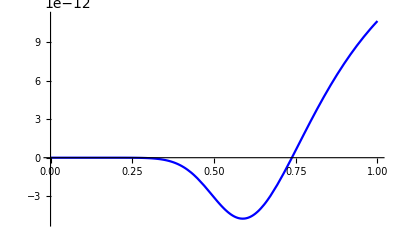

```mathematica
cdotCG/.H0^2 M^2->1/.H0-> 70.9/(2.99792458 10^5);
plotcdot=Plot[%,{a,0,1}, PlotStyle->Blue,PlotRange->{{0,1},{-5 10^(-12),1.1*10^-11}}]
```

```mathematica
cDotEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,9}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-5 10^(-12),1.1*10^-11}}, PlotLabel->"cDot(a)"
]
```

566 lines of corrupt data deleted.

156 lines of corrupt data deleted.

6214 lines of corrupt data deleted.

```mathematica
Show[cDotEFTCAMBPlot,plotcdot]
```

736 lines of corrupt data deleted.

6358 lines of corrupt data deleted.

Gamma 1

```mathematica
gamma1 = 1/(4 a^2 Subscript[H, 0]^2 s^3)(-4 (-1)^-p a^2 Subscript[c, 2] Subscript[H, DS]^2 (-1+p) p s^3 Subscript[χ, DS]^-p ℋ[a]^(2 p) φ'[a]^(2 p)+(-1)^-p ⅈ^(-p/s) √2 a Subscript[c, 3] Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(-(p+2 p s)/(2 s)) ℋ[a]^(p (2+1/s)) φ'[a]^(-1+p (2+1/s)) (ℋ[a] (3 (p-2 s+2 p s) φ'[a]+a s φ''[a])+a s φ'[a] ℋ'[a])+16 (-1)^(-p (1+1/s)) Subscript[c, 5] s^2 Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (2 a (p-2 s+p s) φ''[a]+s ℋ[a] (11 φ'[a]+4 a φ''[a])+a (s+2 p (1+s)) φ'[a] ℋ'[a])-4 (-1)^(-p (1+1/s)) Subscript[c, 4] p (1+s) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(-2+(2 p (1+s))/s) (ℋ[a]^2 (2 (2 s^2-9 p s (1+s)+6 p^2 (1+s)^2) φ'[a]^2+a^2 s (-s+2 p (1+s)) φ''[a]^2+a s φ'[a] ((-3 s+4 p (1+s)) φ''[a]+a s φ'''[a]))+2 a^2 p s (1+s) φ'[a]^2 ℋ'[a]^2+a s ℋ[a] φ'[a] (a (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] ((-s+4 p (1+s)) ℋ'[a]+a s ℋ''[a]))));
```

```mathematica
gamma1CG=gamma1/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
gamma1CG/.H0^2 M^2-> 1
a=.
```

1

0.724023+0. ⅈ

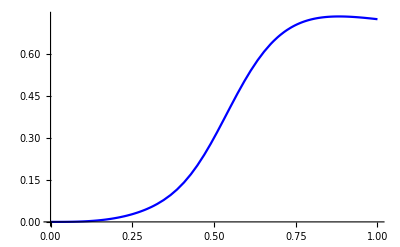

```mathematica
gamma1CG/.H0^2 M^2-> 1;
gamma1plot=Plot[%,{a,0,1},PlotStyle->Blue]
```

```mathematica
dataEFTCAMB2ndOrder=Import[FileNameJoin[{NotebookDirectory[],"QuarticGalileon_SecondOrdEFT.dat"}]]
```

{{1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00010001,0.,0.,2.42776×10^-13,9.82309×10^-9,1.71418×10^-19,9.21737×10^-15,3.83351×10^-25,2.86484×10^-20,-3.83351×10^-25,-2.86484×10^-20,-1.83989×10^-15,1.91676×10^-25,1.43242×10^-20,0.,0.},29996,{1.×10^-10,0.,0.,1.78632×10^-37,7.14527×10^-27,3.53239×10^-55,2.11943×10^-44,7.01496×10^-73,5.61196×10^-62,-7.01496×10^-73,-5.61196×10^-62,-3.92837×10^-51,3.50748×10^-73,2.80598×10^-62,0.,0.},{1.×10^-10,0.,0.,1.78632×10^-37,7.14527×10^-27,3.53239×10^-55,2.11943×10^-44,7.01496×10^-73,5.61196×10^-62,-7.01496×10^-73,-5.61196×10^-62,-3.92837×10^-51,3.50748×10^-73,2.80598×10^-62,0.,0.}}
 |  |  |  |

```mathematica
gamma1EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,4}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotLabel->"Gamma1(a)"
]
```

19 lines of corrupt data deleted.

336 lines of corrupt data deleted.

19 lines of corrupt data deleted.

201 lines of corrupt data deleted.

167 lines of corrupt data deleted.

6074 lines of corrupt data deleted.

```mathematica
Show[gamma1EFTCAMBPlot,gamma1plot]
```

739 lines of corrupt data deleted.

6300 lines of corrupt data deleted.

1315 lines of corrupt data deleted.

292 lines of corrupt data deleted.

```mathematica
gamma1primeCG = gamma1prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562;
```

```mathematica
a=1
gamma1primeCG//Simplify//Expand
%/.√(-H0^4 M^4)->ⅈ H0^2 M^2
gamma1primeCG/.H0->1/.M->1//Simplify//Expand
a=.
```

1

-0.963241-((0.+0.829096 ⅈ) √(-H0^4 M^4))/(H0^2 M^2)

-0.134145+0. ⅈ

-0.134145+0. ⅈ

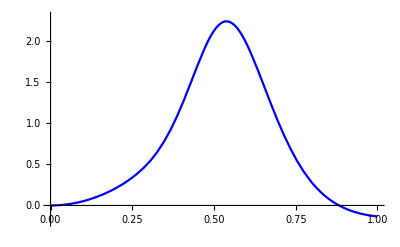

```mathematica
gamma1primeCG/.H0->1/.M->1;
gamma1primeCGplot=Plot[%,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.2,2.3}}]
```

```mathematica
gamma1primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,5}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.2,2.3}}, PlotLabel->"Gamma1'(a)"
]
```

509 lines of corrupt data deleted.

49 lines of corrupt data deleted.

174 lines of corrupt data deleted.

6168 lines of corrupt data deleted.

```mathematica
Show[gamma1primeEFTCAMBPlot,gamma1primeCGplot]
```

738 lines of corrupt data deleted.

6375 lines of corrupt data deleted.

#### gamma2

```mathematica
gamma2 = 1/(a Subscript[H, 0] s^2 φ'[a])(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-√2 a Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(1+p (2+1/s))+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^((2 p (1+s))/s) (2 (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) φ'[a]+a Subscript[c, 4] p s (1+s) φ''[a])+4 (-1)^p ⅈ^(p/s) a Subscript[c, 4] p s (1+s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) ℋ'[a]);
```

```mathematica
gamma2/.p->1/.s->1;
Coefficient[%,c4]//Expand
```

(48 Hconf[a]^5 PhiPrime[a]^4)/(a H0 XDS^2)+(8 Hconf[a]^5 PhiPrime[a]^3 PhiPrimePrime[a])/(H0 XDS^2)+(8 Hconf[a]^4 PhiPrime[a]^4 Hconf'[a])/(H0 XDS^2)

```mathematica
gamma2CG=gamma2/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
gamma2CG/.Subscript[H, 0]^2 M^2->1
a=.
```

1

-0.57043+0. ⅈ

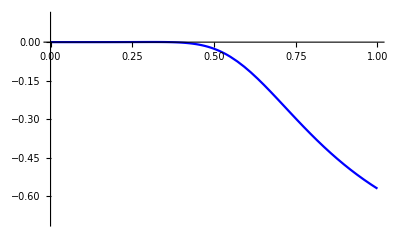

```mathematica
gamma2CG/.H0^2 M^2-> 1;
gamma2plot=Plot[%,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.7,0.1}}]
```

```mathematica
gamma2EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,6}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.7,0.1}}, PlotLabel->"Gamma2(a)"
]
```

290 lines of corrupt data deleted.

149 lines of corrupt data deleted.

29 lines of corrupt data deleted.

12 lines of corrupt data deleted.

28 lines of corrupt data deleted.

227 lines of corrupt data deleted.

6185 lines of corrupt data deleted.

```mathematica
Show[gamma2EFTCAMBPlot,gamma2plot]
```

739 lines of corrupt data deleted.

6412 lines of corrupt data deleted.

```mathematica
gamma2prime = 1/(a^2 Subscript[H, 0] s^3 ℋ[a] φ'[a]^2)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] p s (1+2 s) (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(1+p (2+1/s)) φ''[a]-4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) (2 s (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) φ'[a]^(2 (1+p+p/s))-a^2 Subscript[c, 4] p s (1+s) (-s+2 p (1+s)) φ'[a]^((2 p (1+s))/s) φ''[a]^2-a p (1+s) φ'[a]^(1+(2 p (1+s))/s) (4 (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) φ''[a]+a Subscript[c, 4] s^2 φ'''[a]))-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] p s (1+2 s) (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(2+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 Subscript[c, 4] p^2 s (1+s)^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) (a Subscript[c, 4] p s (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (2 (s+2 p (1+s)) (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s^2 (1+s) ℋ''[a])));
```

```mathematica
gamma2primeCG=gamma2prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562;
```

```mathematica
a=1
gamma2primeCG//Expand
a=.
```

1

(1.96045+0. ⅈ)+((0.+2.76117 ⅈ) √(-H0^2 M^2) √(H0^2 M^2))/(H0^2 M^2)

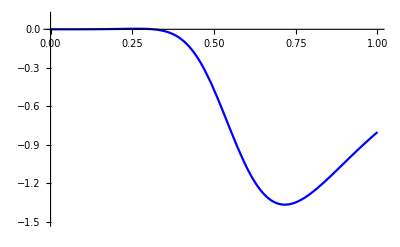

```mathematica
gamma2primeCG//Expand;
%/.H0->1/.M->1;
gamma2primeplot=Plot[%,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-1.5,0.1}}]
```

```mathematica
gamma2primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,7}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-1.5,0.1}}, PlotLabel->"Gamma2'(a)"
]
```

107 lines of corrupt data deleted.

348 lines of corrupt data deleted.

25 lines of corrupt data deleted.

253 lines of corrupt data deleted.

6151 lines of corrupt data deleted.

```mathematica
Show[gamma2primeEFTCAMBPlot,gamma2primeplot]
```

738 lines of corrupt data deleted.

6419 lines of corrupt data deleted.

#### gamma 3

```mathematica
gamma3 = (4 (-1)^(-p (1+1/s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s))/s;
```

```mathematica
gamma3CG=gamma3/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
gamma3CG
a=.
```

1

0.479866

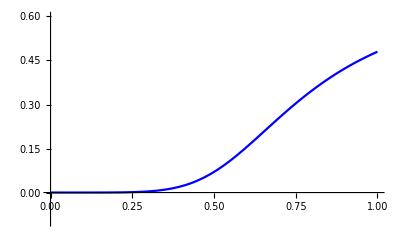

```mathematica
gamma3plot=Plot[gamma3CG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,0.6}}]
```

```mathematica
gamma3EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,8}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,0.6}}, PlotLabel->"Gamma3(a)"
]
```

470 lines of corrupt data deleted.

52 lines of corrupt data deleted.

15 lines of corrupt data deleted.

196 lines of corrupt data deleted.

6169 lines of corrupt data deleted.

```mathematica
Show[gamma3EFTCAMBPlot,gamma3plot]
```

739 lines of corrupt data deleted.

6371 lines of corrupt data deleted.

743 lines of corrupt data deleted.

6347 lines of corrupt data deleted.

```mathematica
gamma3prime = 1/s^2 8 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]);
```

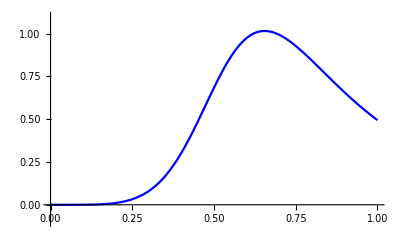

```mathematica
gamma3primeCG=gamma3prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
gamma3primeplot=Plot[gamma3primeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,1.1}}]
```

```mathematica
gamma3primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,9}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,1.1}}, PlotLabel->"Gamma3'(a)"
]
```

489 lines of corrupt data deleted.

239 lines of corrupt data deleted.

6154 lines of corrupt data deleted.

```mathematica
Show[gamma3primeEFTCAMBPlot,gamma3primeplot]
```

738 lines of corrupt data deleted.

6410 lines of corrupt data deleted.

#### gamma 4

```mathematica
gamma4 = -(4 (-1)^(-p (1+1/s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s))/s;
```

```mathematica
gamma4CG=gamma4/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

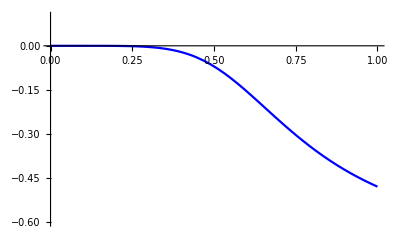

```mathematica
gamma4plot=Plot[gamma4CG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.6,0.1}}]
```

```mathematica
gamma4EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,10}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.6,0.1}}, PlotLabel->"Gamma4(a)"
]
```

477 lines of corrupt data deleted.

55 lines of corrupt data deleted.

200 lines of corrupt data deleted.

6205 lines of corrupt data deleted.

```mathematica
Show[gamma4EFTCAMBPlot,gamma4plot]
```

737 lines of corrupt data deleted.

6408 lines of corrupt data deleted.

```mathematica
gamma4prime = -1/s^2 8 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]);
```

```mathematica
gamma4primeCG=gamma4prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

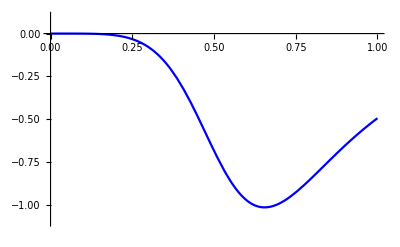

```mathematica
gamma4primeplot=Plot[gamma4primeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-1.1,0.1}}]
```

```mathematica
gamma4primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,11}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-1.1,0.1}}, PlotLabel->"Gamma4'(a)"
]
```

426 lines of corrupt data deleted.

75 lines of corrupt data deleted.

230 lines of corrupt data deleted.

6187 lines of corrupt data deleted.

```mathematica
Show[gamma4primeEFTCAMBPlot,gamma4primeplot]
```

738 lines of corrupt data deleted.

6442 lines of corrupt data deleted.

```mathematica
gamma4primeprime = -1/s^3 8 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-2+(2 p (1+s))/s) φ'[a]^(-2+(2 p (1+s))/s) (ℋ[a]^2 ((-s+2 p (1+s)) φ''[a]^2+s φ'[a] φ'''[a])+(-s+2 p (1+s)) φ'[a]^2 ℋ'[a]^2+ℋ[a] φ'[a] (4 p (1+s) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a]));
```

```mathematica
gamma4primeprimeCG=gamma4primeprime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

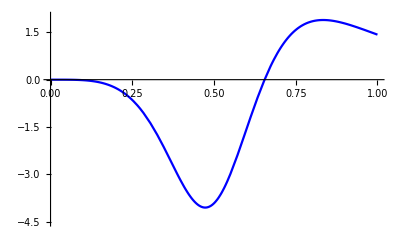

```mathematica
gamma4primeprimeplot=Plot[gamma4primeprimeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-4.5,2}}]
```

```mathematica
gamma4primeprimeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,12}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-4.5,2}}, PlotLabel->"Gamma4''(a)"
]
```

335 lines of corrupt data deleted.

131 lines of corrupt data deleted.

264 lines of corrupt data deleted.

6199 lines of corrupt data deleted.

```mathematica
Show[gamma4primeprimeEFTCAMBPlot,gamma4primeprimeplot]
```

737 lines of corrupt data deleted.

6493 lines of corrupt data deleted.

#### gamma 5

```mathematica
gamma5 = (2 (-1)^(-p (1+1/s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s))/s;
```

```mathematica
gamma5CG=gamma5/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

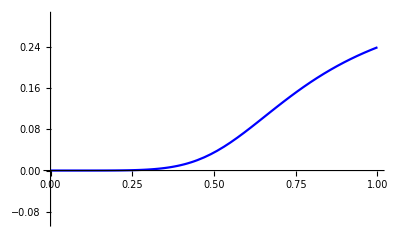

```mathematica
gamma5plot=Plot[gamma5CG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,0.3}}]
```

```mathematica
gamma5EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,13}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,0.3}}, PlotLabel->"Gamma5(a)"
]
```

478 lines of corrupt data deleted.

54 lines of corrupt data deleted.

198 lines of corrupt data deleted.

6158 lines of corrupt data deleted.

```mathematica
Show[gamma5EFTCAMBPlot,gamma5plot]
```

739 lines of corrupt data deleted.

6358 lines of corrupt data deleted.

#### gamma 5

```mathematica
gamma5prime = 1/s^2 4 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]);
```

```mathematica
gamma5primeCG=gamma5prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

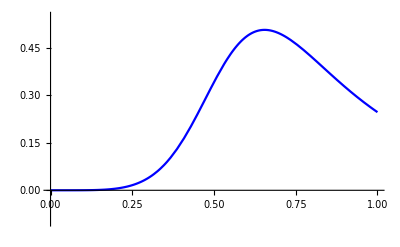

```mathematica
gamma5primeplot=Plot[gamma5primeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,0.55}}]
```

```mathematica
gamma5primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,14}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,0.55}}, PlotLabel->"Gamma5'(a)"
]
```

421 lines of corrupt data deleted.

78 lines of corrupt data deleted.

231 lines of corrupt data deleted.

6155 lines of corrupt data deleted.

```mathematica
Show[gamma5primeEFTCAMBPlot,gamma5primeplot]
```

737 lines of corrupt data deleted.

6407 lines of corrupt data deleted.

```mathematica
a:=A D[f[x],x]
```

```mathematica
a/.f'[x]->xf'[x]
```

A xf'[x]

```mathematica
-(adotoa**4*phip1**4*(-(a*self%WBGalileon_c4*eft_par_cache%h0_Mpc**2*m0)+6*self%WBGalileon_c5*(Hdot*phip1+a*adotoa**2*phip2)))/(2.*a*eft_par_cache%h0_Mpc**6*m0**5)
```

1/(m0**5 h0_Mpc**6)3. A^2 m0 self^2 adotoa**4 phip1**4 h0_Mpc**2 WBGalileon_c4 WBGalileon_c5 (Hdot phip1+A phip2 adotoa**2 f'[x]) xf'[x]^2

6 lines of corrupt data deleted.